```mathematica
c1=Cycles[{{1,60},{2,72},{3,81},{4,43},{5,11},{6,87},{7,34},{9,63},{12,46},{13,28},{14,71},{15,42},{16,97},{18,57},{19,52},{21,32},{23,47},{24,54},{25,83},{26,78},{29,89},{30,39},{33,61},{35,56},{37,67},{44,76},{45,88},{48,59},{49,86},{50,74},{51,66},{53,99},{55,75},{62,73},{65,79},{68,82},{77,92},{84,90},{85,98},{94,100}}]
```

Cycles[{{1,60},{2,72},{3,81},{4,43},{5,11},{6,87},{7,34},{9,63},{12,46},{13,28},{14,71},{15,42},{16,97},{18,57},{19,52},{21,32},{23,47},{24,54},{25,83},{26,78},{29,89},{30,39},{33,61},{35,56},{37,67},{44,76},{45,88},{48,59},{49,86},{50,74},{51,66},{53,99},{55,75},{62,73},{65,79},{68,82},{77,92},{84,90},{85,98},{94,100}}]

```mathematica
c2=Cycles[{{1,86,13,10,47},{2,53,30,8,38},{3,40,48,25,17},{4,29,92,88,43},{5,98,66,54,65},{6,27,51,73,24},{7,83,16,20,28},{9,23,89,95,61},{11,42,46,91,32},{12,14,81,55,68},{15,90,31,56,37},{18,69,45,84,76},{19,59,79,35,93},{21,22,64,39,100},{26,58,96,85,77},{33,52,94,75,44},{34,62,87,78,50},{36,82,60,74,72},{41,80,70,49,67},{57,63,71,99,97}}]
```

Cycles[{{1,86,13,10,47},{2,53,30,8,38},{3,40,48,25,17},{4,29,92,88,43},{5,98,66,54,65},{6,27,51,73,24},{7,83,16,20,28},{9,23,89,95,61},{11,42,46,91,32},{12,14,81,55,68},{15,90,31,56,37},{18,69,45,84,76},{19,59,79,35,93},{21,22,64,39,100},{26,58,96,85,77},{33,52,94,75,44},{34,62,87,78,50},{36,82,60,74,72},{41,80,70,49,67},{57,63,71,99,97}}]

```mathematica
perm =Cycles[{{1,60},{2,72},{3,81},{4,43},{5,11},{6,87},{7,34},{9,63},{12,46},{13,28},{14,71},{15,42},{16,97},{18,57},{19,52},{21,32},{23,47},{24,54},{25,83},{26,78},{29,89},{30,39},{33,61},{35,56},{37,67},{44,76},{45,88},{48,59},{49,86},{50,74},{51,66},{53,99},{55,75},{62,73},{65,79},{68,82},{77,92},{84,90},{85,98},{94,100}}]
rules[cycle_]:=Thread[DirectedEdge[cycle,RotateLeft[cycle]]];
Flatten[rules/@First[perm]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{1,60},{2,72},{3,81},{4,43},{5,11},{6,87},{7,34},{9,63},{12,46},{13,28},{14,71},{15,42},{16,97},{18,57},{19,52},{21,32},{23,47},{24,54},{25,83},{26,78},{29,89},{30,39},{33,61},{35,56},{37,67},{44,76},{45,88},{48,59},{49,86},{50,74},{51,66},{53,99},{55,75},{62,73},{65,79},{68,82},{77,92},{84,90},{85,98},{94,100}}]

{1->60,60->1,2->72,72->2,3->81,81->3,4->43,43->4,5->11,11->5,6->87,87->6,7->34,34->7,9->63,63->9,12->46,46->12,13->28,28->13,14->71,71->14,15->42,42->15,16->97,97->16,18->57,57->18,19->52,52->19,21->32,32->21,23->47,47->23,24->54,54->24,25->83,83->25,26->78,78->26,29->89,89->29,30->39,39->30,33->61,61->33,35->56,56->35,37->67,67->37,44->76,76->44,45->88,88->45,48->59,59->48,49->86,86->49,50->74,74->50,51->66,66->51,53->99,99->53,55->75,75->55,62->73,73->62,65->79,79->65,68->82,82->68,77->92,92->77,84->90,90->84,85->98,98->85,94->100,100->94}

-Graphics-

```mathematica
perm =Cycles[{{1,86,13,10,47},{2,53,30,8,38},{3,40,48,25,17},{4,29,92,88,43},{5,98,66,54,65},{6,27,51,73,24},{7,83,16,20,28},{9,23,89,95,61},{11,42,46,91,32},{12,14,81,55,68},{15,90,31,56,37},{18,69,45,84,76},{19,59,79,35,93},{21,22,64,39,100},{26,58,96,85,77},{33,52,94,75,44},{34,62,87,78,50},{36,82,60,74,72},{41,80,70,49,67},{57,63,71,99,97}}]
rules[cycle_]:=Thread[DirectedEdge[cycle,RotateLeft[cycle]]];
Flatten[rules/@First[perm]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

Cycles[{{1,86,13,10,47},{2,53,30,8,38},{3,40,48,25,17},{4,29,92,88,43},{5,98,66,54,65},{6,27,51,73,24},{7,83,16,20,28},{9,23,89,95,61},{11,42,46,91,32},{12,14,81,55,68},{15,90,31,56,37},{18,69,45,84,76},{19,59,79,35,93},{21,22,64,39,100},{26,58,96,85,77},{33,52,94,75,44},{34,62,87,78,50},{36,82,60,74,72},{41,80,70,49,67},{57,63,71,99,97}}]

{1->86,86->13,13->10,10->47,47->1,2->53,53->30,30->8,8->38,38->2,3->40,40->48,48->25,25->17,17->3,4->29,29->92,92->88,88->43,43->4,5->98,98->66,66->54,54->65,65->5,6->27,27->51,51->73,73->24,24->6,7->83,83->16,16->20,20->28,28->7,9->23,23->89,89->95,95->61,61->9,11->42,42->46,46->91,91->32,32->11,12->14,14->81,81->55,55->68,68->12,15->90,90->31,31->56,56->37,37->15,18->69,69->45,45->84,84->76,76->18,19->59,59->79,79->35,35->93,93->19,21->22,22->64,64->39,39->100,100->21,26->58,58->96,96->85,85->77,77->26,33->52,52->94,94->75,75->44,44->33,34->62,62->87,87->78,78->50,50->34,36->82,82->60,60->74,74->72,72->36,41->80,80->70,70->49,49->67,67->41,57->63,63->71,71->99,99->97,97->57}

-Graphics-

```mathematica
Partition[Permute[Range[100],c2],2]//Column
```

{47,38}
{17,43}
{65,24}
{28,30}
{61,13}
{32,68}
{86,12}
{37,83}
{25,76}
{93,16}
{100,21}
{9,73}
{48,77}
{6,20}
{4,53}
{90,91}
{44,50}
{79,72}
{56,8}
{64,3}
{67,11}
{88,75}
{69,42}
{10,40}
{70,78}
{27,33}
{2,66}
{81,31}
{97,26}
{19,82}
{95,34}
{57,22}
{54,98}
{49,55}
{18,80}
{63,74}
{51,60}
{94,84}
{85,87}
{59,41}
{14,36}
{7,45}
{96,1}
{62,92}
{23,15}
{46,29}
{35,52}
{89,58}
{99,5}
{71,39}

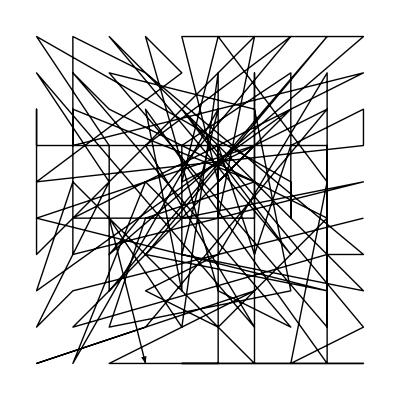
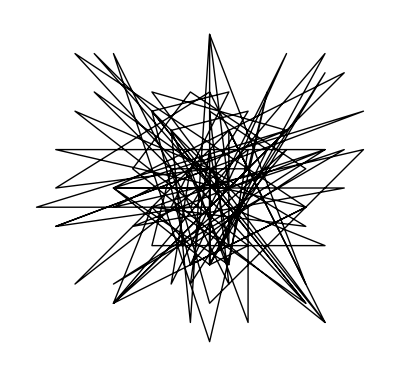
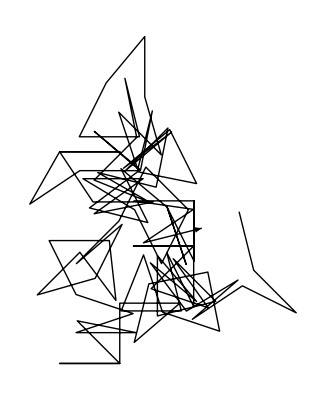
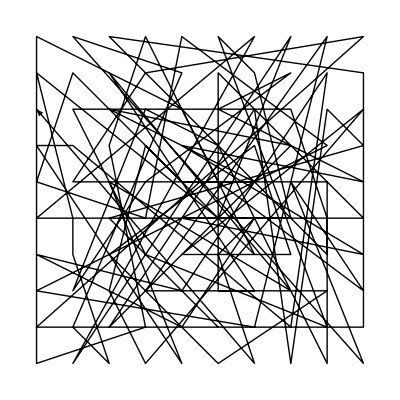
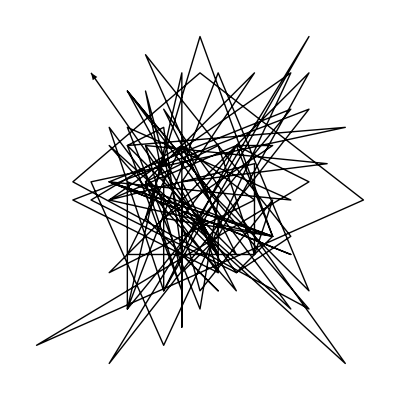
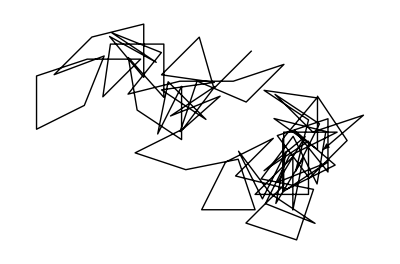
{{(60 | 72 | 81 | 43 | 11 | 87 | 34 | 8 | 63 | 10
5 | 46 | 28 | 71 | 42 | 97 | 17 | 57 | 52 | 20
32 | 22 | 47 | 54 | 83 | 78 | 27 | 13 | 89 | 39
31 | 21 | 61 | 7 | 56 | 36 | 67 | 38 | 30 | 40
41 | 15 | 4 | 76 | 88 | 12 | 23 | 59 | 86 | 74
66 | 19 | 99 | 24 | 75 | 35 | 18 | 58 | 48 | 1
33 | 73 | 9 | 64 | 79 | 51 | 37 | 82 | 69 | 70
14 | 2 | 62 | 50 | 55 | 44 | 92 | 26 | 65 | 80
3 | 68 | 25 | 90 | 98 | 49 | 6 | 45 | 29 | 84
91 | 77 | 93 | 100 | 95 | 96 | 16 | 85 | 53 | 94),{-Graphics-,{{-8,-2},{-1,-1},{2,4},{-2,3},{6,-7},{-3,5},{4,3},{-5,-6},{7,6},{-5,0},{1,-4},{2,2},{-7,-5},{1,3},{5,-5},{0,8},{0,-4},{-5,0},{8,4},{-8,-2},{0,1},{5,-2},{-3,-1},{-1,-3},{5,1},{-1,5},{-4,1},{6,-7},{0,5},{-8,0},{0,1},{0,-4},{6,6},{-1,-5},{0,2},{1,-3},{1,3},{2,1},{0,-1},{-9,-1},{4,3},{-1,1},{2,-7},{2,-1},{-6,7},{1,-1},{6,-3},{-3,-3},{-2,1},{2,1},{3,5},{0,-8},{-5,7},{1,-5},{0,4},{3,2},{0,-4},{0,1},{-7,4},{2,-3},{0,-4},{6,7},{-5,-6},{5,-1},{-8,2},{6,2},{-5,-5},{7,2},{1,0},{-6,5},{-2,1},{0,-6},{8,2},{-5,-1},{-1,1},{-2,-5},{4,7},{-1,-4},{5,-1},{-7,7},{5,-6},{-3,4},{5,-6},{-2,-1},{1,5},{-3,4},{-1,-4},{4,2},{-5,-6},{-3,-1},{6,2},{-4,-2},{7,0},{-5,0},{1,0},{0,8},{-1,-7},{-2,3},{1,-4}},-Graphics-}},-Graphics-}
{{(47 | 38 | 17 | 43 | 65 | 24 | 28 | 30 | 61 | 13
32 | 68 | 86 | 12 | 37 | 83 | 25 | 76 | 93 | 16
100 | 21 | 9 | 73 | 48 | 77 | 6 | 20 | 4 | 53
90 | 91 | 44 | 50 | 79 | 72 | 56 | 8 | 64 | 3
67 | 11 | 88 | 75 | 69 | 42 | 10 | 40 | 70 | 78
27 | 33 | 2 | 66 | 81 | 31 | 97 | 26 | 19 | 82
95 | 34 | 57 | 22 | 54 | 98 | 49 | 55 | 18 | 80
63 | 74 | 51 | 60 | 94 | 84 | 85 | 87 | 59 | 41
14 | 36 | 7 | 45 | 96 | 1 | 62 | 92 | 23 | 15
46 | 29 | 35 | 52 | 89 | 58 | 99 | 5 | 71 | 39),{-Graphics-,{{-3,3},{7,2},{-1,1},{-1,-7},{-1,7},{-4,-6},{5,5},{-5,1},{4,-2},{-5,0},{2,3},{6,1},{-9,-8},{9,0},{0,7},{-7,1},{6,-6},{0,1},{-1,3},{-6,0},{2,-4},{5,-2},{-3,8},{1,-1},{1,-4},{-7,0},{6,5},{-5,-9},{6,9},{-2,-5},{-5,4},{1,-4},{0,-1},{1,-3},{-1,1},{3,7},{-3,1},{8,-9},{-2,5},{2,-3},{-4,3},{-2,4},{-1,-3},{1,-5},{-3,-1},{0,9},{4,-2},{2,-4},{-3,3},{-1,-4},{1,-2},{6,7},{-5,-4},{3,0},{-1,3},{-4,-3},{3,-3},{3,2},{-5,0},{5,7},{-2,-8},{-6,1},{8,4},{-4,3},{-1,-5},{-3,1},{1,3},{3,-3},{4,0},{0,-5},{-3,6},{-2,1},{-2,-5},{2,3},{4,3},{-2,-1},{4,-2},{-5,1},{5,-3},{-5,1},{5,0},{-4,4},{0,-6},{1,0},{-4,6},{5,-6},{-5,3},{2,-5},{-4,6},{1,0},{6,-5},{1,7},{-4,-6},{-4,1},{4,-2},{2,3},{-1,-1},{1,-3},{-6,7}},-Graphics-}},-Graphics-}

```mathematica
Map[{GM[#],matuni[#]}&,{Partition[Permute[Range[100],c1],10],Partition[Permute[Range[100],c2],10]}]//Column
```

```mathematica
GraphData["HigmanSimsGraph"]
```

-Graphics-

```mathematica
Normal[GraphData["HigmanSimsGraph","AdjacencyMatrix"]]//ArrayPlot
```

-Graphics-

```mathematica
Monitor[Table[Table[Normal[GraphData["HigmanSimsGraph","AdjacencyMatrix"]][[i,j]],{i,1,j}],{j,1,100}],{j,i}]
```

{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0},{0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,1,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0},{1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0},{1,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{1,0,1,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0},{1,0,0,0,1,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,1,0,0,1,1,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{1,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,1,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,1,0,1,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,1,1,0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,1,1,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,0,1,1,1,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,1,0,0,0,1,0,1,1,0,0,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}}

```mathematica
Map[FromDigits[#,2]&,%]
```

```mathematica
{252,10780,26952,32000,662560,1590464,1623552,9704704,7095296,42542080,47235072,206086144,227049472,707526656,1285619712,3273916416,42969727254,51649185184,206328825248,207781675104,1239238591648,2751132108416,3324456018048,5542118887424,26428142306304,52828771201024,88262654560256,158953527640064,635523660095538,1205104540418200,448773348687968,1495362393343008,10275109059433088,22662070743093312,14356609074479232,90374375517291008,155419302294507520,315397704337860616,867261864124416016,1739542053645254912,1378190168732991872,5337188975671067648,6124950198289957056,23373708593448820746,39456054512307405828,17438048395539256512,60618541161607988352,378738123300426350592,450793188059292702848,1791678383430079873032,1384948373653238612488,3049480762092387844112,10724480658384174977024,15053991247435003855362,57862878608803769614336,26655601516707875782720,302231310788469217820672,585573732101814111698944,639881198869586156453888,646374551869327224602624,647850820556638578802688,2457255058924447180767232,1513742431907523559452672,1817006930376679603886080,38733072462934977748486144,19986542244828826834126848,10389427686315618762104832,309685716207250725476585472,81019327405583104831971328,165775724532683716139483136,631229910411243655741636608,1392848161951209507480141824,1398142891771179231223349248,10213252106451433149138468864,19967303622087241227198529536,5726235640347085344547536896,158778051927939846438918291456,25082871129366367963956903936,8388606}
```

```mathematica
Table[{i,GraphData["HigmanSimsGraph",i]},{i,{"AdjacencyMatrix","AllImages","AllVertexCoordinates","ArcTransitivity","ArcTransitivity","ArticulationVertices","ArticulationVertices","AutomorphismCount","AutomorphismCount","Automorphisms","Automorphisms","Bridges","Bridges","CharacteristicPolynomial","ChromaticallyUnique","ChromaticInvariant","ChromaticNumber","ChromaticPolynomial","CliqueNumber","CliqueNumber","ComplementGraph","Connected","ConnectedComponentCount","ConnectedComponentGraphNames","ConnectedComponentIndices","Corank","Corank","CrossingNumber","CrossingNumber","Degrees","Degrees","DeterminedByResistance","DeterminedByResistance","DeterminedBySpectrum","DeterminedBySpectrum","DetourMatrix","DetourMatrix","DetourPolynomial","Diameter","Diameter","Disconnected","DistanceMatrix","DistancePolynomial","DualGraph","Eccentricities","Eccentricities","EdgeChromaticNumber","EdgeConnectivity","EdgeCount","EdgeIndices","EdgeRules","FaceCount","FaceIndices","FlowPolynomial","Genus","Genus","Girth","Girth","Graph","HamiltonianCycleCount","HamiltonianCycleCount","HamiltonianCycles","HamiltonianCycles","HamiltonianPathCount","HamiltonianPathCount","HamiltonianPaths","HamiltonianPaths","IdiosyncraticPolynomial","Image","Image3D","IncidenceMatrix","IndependenceNumber","IndependenceNumber","IndependencePolynomial","LabeledImage","LaplacianMatrix","LaplacianPolynomial","LineGraph","LovaszNumber","LovaszNumber","MatchingGeneratingPolynomial","MatchingPolynomial","NormalizedLaplacianMatrix","Rank","Rank","RankPolynomial","RectilinearCrossingNumber","RectilinearCrossingNumber","ReliabilityPolynomial","ResistanceMatrix","ResistanceMatrix","ShannonCapacity","ShannonCapacity","SigmaPolynomial","SpanningTreeCount","SpanningTreeCount","Spectrum","Spectrum","ToroidalCrossingNumber","ToroidalCrossingNumber","Triangulated","TuttePolynomial","Unitransitivity","Unitransitivity","VertexConnectivity","VertexCoordinates","VertexCount"}}]//Column
```

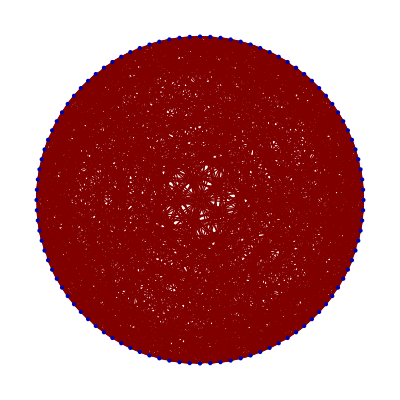
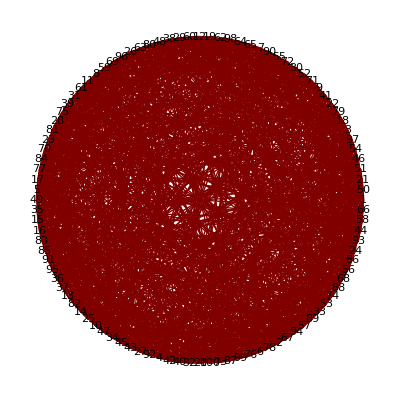
```mathematica
{{{"AdjacencyMatrix",SparseArray["<"2200">",{100,100}]}}, {{"AllImages",{-Graphics-}}}, {{"AllVertexCoordinates",{{{1.12,0.571429},{0.835714,0.0907143},{1.06786,0.805},{0.435,0.0401429},{0.024,0.605857},{0.773429,0.0614286},{0.773429,1.08143},{0.221714,0.994143},{0.971286,0.947},{0.221714,0.148714},{0.195857,0.971286},{0.571429,1.12},{0.127571,0.249},{0.171571,0.195857},{0.0271429,0.502714},{0.0325714,0.468571},{0.0271429,0.640143},{1.05214,0.835714},{0.605857,1.11886},{0.571429,0.0228571},{1.11571,0.640143},{1.01529,0.893857},{0.0614286,0.773429},{1.09314,0.401857},{0.195857,0.171571},{0.337857,1.06786},{0.369429,0.0614286},{0.0907143,0.835714},{0.502714,1.11571},{0.893857,1.01529},{0.148714,0.921143},{0.537,0.024},{0.971286,0.195857},{0.277429,0.108286},{0.024,0.537},{0.0907143,0.307143},{0.108286,0.277429},{0.468571,1.11029},{0.127571,0.893857},{0.502714,0.0271429},{0.994143,0.921143},{0.468571,0.0325714},{0.337857,0.075},{1.11029,0.468571},{0.307143,0.0907143},{1.10271,0.707857},{0.249,0.127571},{0.435,1.10271},{0.0228571,0.571429},{1.11886,0.605857},{1.11029,0.674286},{0.921143,0.994143},{0.994143,0.221714},{1.09314,0.741},{0.835714,1.05214},{1.06786,0.337857},{0.921143,0.148714},{1.11571,0.502714},{0.249,1.01529},{0.537,1.11886},{0.171571,0.947},{0.640143,1.11571},{0.369429,1.08143},{0.707857,1.10271},{0.741,1.09314},{1.11886,0.537},{0.865429,0.108286},{1.05214,0.307143},{0.277429,1.03457},{0.0497143,0.741},{0.947,0.971286},{0.865429,1.03457},{0.640143,0.0271429},{1.01529,0.249},{0.108286,0.865429},{0.741,0.0497143},{0.0325714,0.674286},{0.805,0.075},{1.03457,0.865429},{0.401857,1.09314},{0.075,0.805},{0.148714,0.221714},{0.0401429,0.435},{0.0401429,0.707857},{0.0497143,0.401857},{1.08143,0.369429},{0.674286,0.0325714},{1.03457,0.277429},{0.947,0.171571},{0.805,1.06786},{0.0614286,0.369429},{0.401857,0.0497143},{1.10271,0.435},{0.893857,0.127571},{0.075,0.337857},{0.307143,1.05214},{1.08143,0.773429},{0.674286,1.11029},{0.707857,0.0401429},{0.605857,0.024}}}}}, {{"ArcTransitivity",2}}, {{"ArcTransitivity",2}}, {{"ArticulationVertices",{}}}, {{"ArticulationVertices",{}}}, {{"AutomorphismCount",88704000}}, {{"AutomorphismCount",88704000}}, {{"Automorphisms",Missing["TooLarge"]}}, {{"Automorphisms",Missing["TooLarge"]}}, {{"Bridges",{}}}, {{"Bridges",{}}}, {{"CharacteristicPolynomial",(-22+#1) (-2+#1)^77 (8+#1)^22&}}, {{"ChromaticallyUnique",Missing["NotAvailable"]}}, {{"ChromaticInvariant",Missing["NotAvailable"]}}, {{"ChromaticNumber",Missing["NotAvailable"]}}, {{"ChromaticPolynomial",Missing["NotAvailable"]}}, {{"CliqueNumber",2}}, {{"CliqueNumber",2}}, {{"ComplementGraph",-Graphics-}}, {{"Connected",True}}, {{"ConnectedComponentCount",1}}, {{"ConnectedComponentGraphNames",{"HigmanSimsGraph"}}}, {{"ConnectedComponentIndices",{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}}}}, {{"Corank",1001}}, {{"Corank",1001}}, {{"CrossingNumber",Missing["NotAvailable"]}}, {{"CrossingNumber",Missing["NotAvailable"]}}, {{"Degrees",{22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22}}}, {{"Degrees",{22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22}}}, {{"DeterminedByResistance",Missing["NotAvailable"]}}, {{"DeterminedByResistance",Missing["NotAvailable"]}}, {{"DeterminedBySpectrum",True}}, {{"DeterminedBySpectrum",True}}, {{"DetourMatrix",Missing["NotAvailable"]}}, {{"DetourMatrix",Missing["NotAvailable"]}}, {{"DetourPolynomial",Missing["NotAvailable"]}}, {{"Diameter",2}}, {{"Diameter",2}}, {{"Disconnected",False}}, {{"DistanceMatrix",Missing["TooLarge"]}}, {{"DistancePolynomial",(-176+#1) (-6+#1)^22 (4+#1)^77&}}, {{"DualGraph",Missing["NotAvailable"]}}, {{"Eccentricities",{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}, {{"Eccentricities",{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}, {{"EdgeChromaticNumber",Missing["NotAvailable"]}}, {{"EdgeConnectivity",22}}, {{"EdgeCount",1100}}, {{"EdgeIndices",{{1,50},{1,51},{1,54},{1,55},{1,57},{1,58},{1,59},{1,60},{1,61},{1,63},{1,65},{1,66},{1,69},{1,71},{1,74},{1,76},{1,78},{1,79},{1,80},{1,86},{1,89},{1,98},{2,42},{2,43},{2,46},{2,47},{2,48},{2,49},{2,60},{2,61},{2,62},{2,64},{2,70},{2,71},{2,72},{2,73},{2,75},{2,76},{2,78},{2,79},{2,81},{2,83},{2,95},{2,96},{3,38},{3,40},{3,44},{3,45},{3,46},{3,47},{3,53},{3,55},{3,56},{3,57},{3,65},{3,68},{3,69},{3,70},{3,75},{3,77},{3,78},{3,79},{3,82},{3,87},{3,92},{3,93},{4,39},{4,40},{4,41},{4,43},{4,44},{4,48},{4,50},{4,52},{4,54},{4,56},{4,63},{4,64},{4,67},{4,68},{4,73},{4,74},{4,78},{4,79},{4,84},{4,90},{4,91},{4,94},{5,38},{5,39},{5,41},{5,42},{5,45},{5,49},{5,51},{5,52},{5,53},{5,58},{5,59},{5,62},{5,66},{5,67},{5,72},{5,77},{5,78},{5,79},{5,85},{5,88},{5,97},{5,99},{6,29},{6,31},{6,33},{6,35},{6,36},{6,37},{6,59},{6,62},{6,63},{6,64},{6,67},{6,68},{6,69},{6,75},{6,76},{6,77},{6,78},{6,80},{6,81},{6,84},{6,85},{6,93},{7,26},{7,27},{7,32},{7,33},{7,34},{7,37},{7,53},{7,54},{7,56},{7,58},{7,65},{7,67},{7,71},{7,72},{7,73},{7,75},{7,78},{7,80},{7,82},{7,94},{7,95},{7,99},{8,27},{8,28},{8,30},{8,31},{8,34},{8,35},{8,51},{8,52},{8,55},{8,56},{8,61},{8,64},{8,70},{8,72},{8,74},{8,77},{8,78},{8,80},{8,83},{8,87},{8,91},{8,97},{9,26},{9,28},{9,29},{9,30},{9,32},{9,36},{9,50},{9,52},{9,53},{9,57},{9,60},{9,62},{9,66},{9,68},{9,70},{9,73},{9,78},{9,80},{9,88},{9,90},{9,92},{9,96},{10,23},{10,24},{10,32},{10,34},{10,35},{10,36},{10,44},{10,45},{10,48},{10,49},{10,66},{10,67},{10,69},{10,70},{10,71},{10,74},{10,78},{10,81},{10,82},{10,90},{10,97},{10,98},{11,24},{11,25},{11,29},{11,30},{11,33},{11,34},{11,41},{11,42},{11,44},{11,46},{11,61},{11,63},{11,65},{11,66},{11,73},{11,77},{11,78},{11,81},{11,86},{11,91},{11,92},{11,99},{12,23},{12,25},{12,30},{12,31},{12,32},{12,37},{12,41},{12,43},{12,45},{12,47},{12,59},{12,60},{12,65},{12,68},{12,72},{12,74},{12,78},{12,81},{12,87},{12,88},{12,89},{12,94},{13,24},{13,25},{13,27},{13,28},{13,36},{13,37},{13,39},{13,40},{13,47},{13,49},{13,57},{13,58},{13,73},{13,74},{13,76},{13,77},{13,78},{13,82},{13,83},{13,84},{13,86},{13,88},{14,23},{14,25},{14,26},{14,28},{14,33},{14,35},{14,38},{14,39},{14,46},{14,48},{14,54},{14,55},{14,66},{14,68},{14,72},{14,76},{14,78},{14,82},{14,85},{14,89},{14,91},{14,96},{15,22},{15,25},{15,26},{15,31},{15,34},{15,36},{15,40},{15,42},{15,45},{15,48},{15,52},{15,55},{15,58},{15,60},{15,63},{15,75},{15,78},{15,83},{15,85},{15,92},{15,94},{15,98},{16,22},{16,24},{16,26},{16,30},{16,35},{16,37},{16,39},{16,43},{16,45},{16,46},{16,51},{16,56},{16,57},{16,62},{16,63},{16,71},{16,78},{16,83},{16,89},{16,90},{16,93},{16,99},{17,22},{17,25},{17,27},{17,29},{17,32},{17,35},{17,38},{17,43},{17,44},{17,49},{17,52},{17,54},{17,57},{17,59},{17,61},{17,75},{17,78},{17,84},{17,87},{17,96},{17,98},{17,99},{18,22},{18,24},{18,28},{18,31},{18,32},{18,33},{18,38},{18,41},{18,47},{18,48},{18,50},{18,56},{18,58},{18,61},{18,62},{18,69},{18,78},{18,84},{18,89},{18,92},{18,95},{18,97},{19,22},{19,23},{19,28},{19,29},{19,34},{19,37},{19,40},{19,41},{19,46},{19,49},{19,51},{19,53},{19,54},{19,60},{19,64},{19,69},{19,78},{19,85},{19,86},{19,87},{19,90},{19,95},{20,22},{20,23},{20,27},{20,30},{20,33},{20,36},{20,39},{20,42},{20,44},{20,47},{20,50},{20,53},{20,55},{20,59},{20,64},{20,71},{20,78},{20,86},{20,93},{20,94},{20,96},{20,97},{21,23},{21,24},{21,26},{21,27},{21,29},{21,31},{21,38},{21,40},{21,42},{21,43},{21,50},{21,51},{21,65},{21,67},{21,70},{21,76},{21,78},{21,88},{21,91},{21,93},{21,95},{21,98},{22,65},{22,66},{22,67},{22,68},{22,70},{22,72},{22,73},{22,74},{22,76},{22,77},{22,79},{22,80},{22,81},{22,82},{22,88},{22,91},{23,52},{23,56},{23,57},{23,58},{23,61},{23,62},{23,63},{23,73},{23,75},{23,77},{23,79},{23,80},{23,83},{23,84},{23,92},{23,99},{24,52},{24,53},{24,54},{24,55},{24,59},{24,60},{24,64},{24,68},{24,72},{24,75},{24,79},{24,80},{24,85},{24,87},{24,94},{24,96},{25,50},{25,51},{25,53},{25,56},{25,62},{25,64},{25,67},{25,69},{25,70},{25,71},{25,79},{25,80},{25,90},{25,93},{25,95},{25,97},{26,41},{26,44},{26,47},{26,49},{26,59},{26,61},{26,64},{26,69},{26,74},{26,77},{26,79},{26,81},{26,84},{26,86},{26,87},{26,97},{27,41},{27,45},{27,46},{27,48},{27,60},{27,62},{27,63},{27,66},{27,68},{27,69},{27,79},{27,81},{27,85},{27,89},{27,90},{27,92},{28,42},{28,43},{28,44},{28,45},{28,59},{28,63},{28,65},{28,67},{28,71},{28,75},{28,79},{28,81},{28,93},{28,94},{28,98},{28,99},{29,39},{29,45},{29,47},{29,48},{29,55},{29,56},{29,58},{29,71},{29,72},{29,74},{29,79},{29,82},{29,83},{29,89},{29,94},{29,97},{30,38},{30,40},{30,48},{30,49},{30,54},{30,58},{30,67},{30,69},{30,75},{30,76},{30,79},{30,82},{30,84},{30,85},{30,95},{30,98},{31,39},{31,44},{31,46},{31,49},{31,53},{31,54},{31,57},{31,66},{31,71},{31,73},{31,79},{31,82},{31,86},{31,90},{31,96},{31,99},{32,39},{32,40},{32,42},{32,46},{32,51},{32,55},{32,63},{32,64},{32,76},{32,77},{32,79},{32,83},{32,85},{32,86},{32,91},{32,93},{33,40},{33,43},{33,45},{33,49},{33,51},{33,52},{33,57},{33,60},{33,70},{33,74},{33,79},{33,83},{33,87},{33,88},{33,90},{33,98},{34,38},{34,39},{34,43},{34,47},{34,50},{34,57},{34,59},{34,62},{34,68},{34,76},{34,79},{34,84},{34,88},{34,89},{34,93},{34,96},{35,40},{35,41},{35,42},{35,47},{35,50},{35,53},{35,58},{35,60},{35,65},{35,73},{35,79},{35,86},{35,88},{35,92},{35,94},{35,95},{36,38},{36,41},{36,43},{36,46},{36,51},{36,54},{36,56},{36,61},{36,65},{36,72},{36,79},{36,87},{36,89},{36,91},{36,95},{36,99},{37,38},{37,42},{37,44},{37,48},{37,50},{37,52},{37,55},{37,61},{37,66},{37,70},{37,79},{37,91},{37,92},{37,96},{37,97},{37,98},{38,60},{38,63},{38,64},{38,71},{38,73},{38,74},{38,80},{38,81},{38,83},{38,86},{38,90},{38,94},{39,60},{39,61},{39,65},{39,69},{39,70},{39,75},{39,80},{39,81},{39,87},{39,92},{39,95},{39,98},{40,59},{40,61},{40,62},{40,66},{40,71},{40,72},{40,80},{40,81},{40,89},{40,96},{40,97},{40,99},{41,55},{41,57},{41,70},{41,71},{41,75},{41,76},{41,80},{41,82},{41,83},{41,93},{41,96},{41,98},{42,54},{42,56},{42,57},{42,68},{42,69},{42,74},{42,80},{42,82},{42,84},{42,87},{42,89},{42,90},{43,53},{43,55},{43,58},{43,66},{43,69},{43,77},{43,80},{43,82},{43,85},{43,86},{43,92},{43,97},{44,51},{44,58},{44,60},{44,62},{44,72},{44,76},{44,80},{44,83},{44,85},{44,88},{44,89},{44,95},{45,50},{45,54},{45,61},{45,64},{45,73},{45,76},{45,80},{45,84},{45,86},{45,91},{45,95},{45,96},{46,50},{46,52},{46,58},{46,59},{46,67},{46,74},{46,80},{46,84},{46,88},{46,94},{46,97},{46,98},{47,51},{47,52},{47,54},{47,63},{47,66},{47,67},{47,80},{47,85},{47,90},{47,91},{47,98},{47,99},{48,51},{48,53},{48,57},{48,59},{48,65},{48,77},{48,80},{48,86},{48,87},{48,88},{48,93},{48,99},{49,50},{49,55},{49,56},{49,63},{49,65},{49,68},{49,80},{49,89},{49,91},{49,92},{49,93},{49,94},{50,72},{50,75},{50,77},{50,81},{50,82},{50,83},{50,85},{50,87},{50,99},{51,68},{51,73},{51,75},{51,81},{51,82},{51,84},{51,92},{51,94},{51,96},{52,65},{52,69},{52,71},{52,76},{52,81},{52,82},{52,86},{52,89},{52,93},{52,95},{53,61},{53,63},{53,74},{53,76},{53,81},{53,83},{53,84},{53,89},{53,91},{53,98},{54,62},{54,70},{54,77},{54,81},{54,83},{54,88},{54,92},{54,93},{54,97},{55,62},{55,67},{55,73},{55,81},{55,84},{55,88},{55,90},{55,95},{55,99},{56,59},{56,60},{56,66},{56,76},{56,81},{56,85},{56,86},{56,88},{56,96},{56,98},{57,64},{57,67},{57,72},{57,81},{57,85},{57,91},{57,94},{57,95},{57,97},{58,64},{58,68},{58,70},{58,81},{58,87},{58,90},{58,91},{58,93},{58,96},{59,70},{59,73},{59,82},{59,83},{59,90},{59,91},{59,92},{59,95},{60,67},{60,77},{60,82},{60,84},{60,91},{60,93},{60,97},{60,99},{61,67},{61,68},{61,82},{61,85},{61,88},{61,90},{61,93},{61,94},{62,65},{62,74},{62,82},{62,86},{62,87},{62,91},{62,94},{62,98},{63,70},{63,72},{63,82},{63,87},{63,88},{63,95},{63,96},{63,97},{64,65},{64,66},{64,82},{64,88},{64,89},{64,92},{64,98},{64,99},{65,83},{65,84},{65,85},{65,90},{65,96},{65,97},{66,75},{66,83},{66,84},{66,87},{66,93},{66,94},{66,95},{67,83},{67,86},{67,87},{67,89},{67,92},{67,96},{68,71},{68,83},{68,86},{68,95},{68,97},{68,98},{68,99},{69,72},{69,73},{69,83},{69,88},{69,91},{69,94},{69,96},{69,99},{70,84},{70,85},{70,86},{70,89},{70,94},{70,99},{71,77},{71,84},{71,85},{71,87},{71,88},{71,91},{71,92},{72,84},{72,86},{72,90},{72,92},{72,93},{72,98},{73,85},{73,87},{73,89},{73,93},{73,97},{73,98},{74,75},{74,85},{74,92},{74,93},{74,95},{74,96},{74,99},{75,86},{75,88},{75,89},{75,90},{75,91},{75,97},{76,87},{76,90},{76,92},{76,94},{76,97},{76,99},{77,89},{77,90},{77,94},{77,95},{77,96},{77,98},{78,100},{79,100},{80,100},{81,100},{82,100},{83,100},{84,100},{85,100},{86,100},{87,100},{88,100},{89,100},{90,100},{91,100},{92,100},{93,100},{94,100},{95,100},{96,100},{97,100},{98,100},{99,100}}}}, {{"EdgeRules",{1->50,1->51,1->54,1->55,1->57,1->58,1->59,1->60,1->61,1->63,1->65,1->66,1->69,1->71,1->74,1->76,1->78,1->79,1->80,1->86,1->89,1->98,2->42,2->43,2->46,2->47,2->48,2->49,2->60,2->61,2->62,2->64,2->70,2->71,2->72,2->73,2->75,2->76,2->78,2->79,2->81,2->83,2->95,2->96,3->38,3->40,3->44,3->45,3->46,3->47,3->53,3->55,3->56,3->57,3->65,3->68,3->69,3->70,3->75,3->77,3->78,3->79,3->82,3->87,3->92,3->93,4->39,4->40,4->41,4->43,4->44,4->48,4->50,4->52,4->54,4->56,4->63,4->64,4->67,4->68,4->73,4->74,4->78,4->79,4->84,4->90,4->91,4->94,5->38,5->39,5->41,5->42,5->45,5->49,5->51,5->52,5->53,5->58,5->59,5->62,5->66,5->67,5->72,5->77,5->78,5->79,5->85,5->88,5->97,5->99,6->29,6->31,6->33,6->35,6->36,6->37,6->59,6->62,6->63,6->64,6->67,6->68,6->69,6->75,6->76,6->77,6->78,6->80,6->81,6->84,6->85,6->93,7->26,7->27,7->32,7->33,7->34,7->37,7->53,7->54,7->56,7->58,7->65,7->67,7->71,7->72,7->73,7->75,7->78,7->80,7->82,7->94,7->95,7->99,8->27,8->28,8->30,8->31,8->34,8->35,8->51,8->52,8->55,8->56,8->61,8->64,8->70,8->72,8->74,8->77,8->78,8->80,8->83,8->87,8->91,8->97,9->26,9->28,9->29,9->30,9->32,9->36,9->50,9->52,9->53,9->57,9->60,9->62,9->66,9->68,9->70,9->73,9->78,9->80,9->88,9->90,9->92,9->96,10->23,10->24,10->32,10->34,10->35,10->36,10->44,10->45,10->48,10->49,10->66,10->67,10->69,10->70,10->71,10->74,10->78,10->81,10->82,10->90,10->97,10->98,11->24,11->25,11->29,11->30,11->33,11->34,11->41,11->42,11->44,11->46,11->61,11->63,11->65,11->66,11->73,11->77,11->78,11->81,11->86,11->91,11->92,11->99,12->23,12->25,12->30,12->31,12->32,12->37,12->41,12->43,12->45,12->47,12->59,12->60,12->65,12->68,12->72,12->74,12->78,12->81,12->87,12->88,12->89,12->94,13->24,13->25,13->27,13->28,13->36,13->37,13->39,13->40,13->47,13->49,13->57,13->58,13->73,13->74,13->76,13->77,13->78,13->82,13->83,13->84,13->86,13->88,14->23,14->25,14->26,14->28,14->33,14->35,14->38,14->39,14->46,14->48,14->54,14->55,14->66,14->68,14->72,14->76,14->78,14->82,14->85,14->89,14->91,14->96,15->22,15->25,15->26,15->31,15->34,15->36,15->40,15->42,15->45,15->48,15->52,15->55,15->58,15->60,15->63,15->75,15->78,15->83,15->85,15->92,15->94,15->98,16->22,16->24,16->26,16->30,16->35,16->37,16->39,16->43,16->45,16->46,16->51,16->56,16->57,16->62,16->63,16->71,16->78,16->83,16->89,16->90,16->93,16->99,17->22,17->25,17->27,17->29,17->32,17->35,17->38,17->43,17->44,17->49,17->52,17->54,17->57,17->59,17->61,17->75,17->78,17->84,17->87,17->96,17->98,17->99,18->22,18->24,18->28,18->31,18->32,18->33,18->38,18->41,18->47,18->48,18->50,18->56,18->58,18->61,18->62,18->69,18->78,18->84,18->89,18->92,18->95,18->97,19->22,19->23,19->28,19->29,19->34,19->37,19->40,19->41,19->46,19->49,19->51,19->53,19->54,19->60,19->64,19->69,19->78,19->85,19->86,19->87,19->90,19->95,20->22,20->23,20->27,20->30,20->33,20->36,20->39,20->42,20->44,20->47,20->50,20->53,20->55,20->59,20->64,20->71,20->78,20->86,20->93,20->94,20->96,20->97,21->23,21->24,21->26,21->27,21->29,21->31,21->38,21->40,21->42,21->43,21->50,21->51,21->65,21->67,21->70,21->76,21->78,21->88,21->91,21->93,21->95,21->98,22->65,22->66,22->67,22->68,22->70,22->72,22->73,22->74,22->76,22->77,22->79,22->80,22->81,22->82,22->88,22->91,23->52,23->56,23->57,23->58,23->61,23->62,23->63,23->73,23->75,23->77,23->79,23->80,23->83,23->84,23->92,23->99,24->52,24->53,24->54,24->55,24->59,24->60,24->64,24->68,24->72,24->75,24->79,24->80,24->85,24->87,24->94,24->96,25->50,25->51,25->53,25->56,25->62,25->64,25->67,25->69,25->70,25->71,25->79,25->80,25->90,25->93,25->95,25->97,26->41,26->44,26->47,26->49,26->59,26->61,26->64,26->69,26->74,26->77,26->79,26->81,26->84,26->86,26->87,26->97,27->41,27->45,27->46,27->48,27->60,27->62,27->63,27->66,27->68,27->69,27->79,27->81,27->85,27->89,27->90,27->92,28->42,28->43,28->44,28->45,28->59,28->63,28->65,28->67,28->71,28->75,28->79,28->81,28->93,28->94,28->98,28->99,29->39,29->45,29->47,29->48,29->55,29->56,29->58,29->71,29->72,29->74,29->79,29->82,29->83,29->89,29->94,29->97,30->38,30->40,30->48,30->49,30->54,30->58,30->67,30->69,30->75,30->76,30->79,30->82,30->84,30->85,30->95,30->98,31->39,31->44,31->46,31->49,31->53,31->54,31->57,31->66,31->71,31->73,31->79,31->82,31->86,31->90,31->96,31->99,32->39,32->40,32->42,32->46,32->51,32->55,32->63,32->64,32->76,32->77,32->79,32->83,32->85,32->86,32->91,32->93,33->40,33->43,33->45,33->49,33->51,33->52,33->57,33->60,33->70,33->74,33->79,33->83,33->87,33->88,33->90,33->98,34->38,34->39,34->43,34->47,34->50,34->57,34->59,34->62,34->68,34->76,34->79,34->84,34->88,34->89,34->93,34->96,35->40,35->41,35->42,35->47,35->50,35->53,35->58,35->60,35->65,35->73,35->79,35->86,35->88,35->92,35->94,35->95,36->38,36->41,36->43,36->46,36->51,36->54,36->56,36->61,36->65,36->72,36->79,36->87,36->89,36->91,36->95,36->99,37->38,37->42,37->44,37->48,37->50,37->52,37->55,37->61,37->66,37->70,37->79,37->91,37->92,37->96,37->97,37->98,38->60,38->63,38->64,38->71,38->73,38->74,38->80,38->81,38->83,38->86,38->90,38->94,39->60,39->61,39->65,39->69,39->70,39->75,39->80,39->81,39->87,39->92,39->95,39->98,40->59,40->61,40->62,40->66,40->71,40->72,40->80,40->81,40->89,40->96,40->97,40->99,41->55,41->57,41->70,41->71,41->75,41->76,41->80,41->82,41->83,41->93,41->96,41->98,42->54,42->56,42->57,42->68,42->69,42->74,42->80,42->82,42->84,42->87,42->89,42->90,43->53,43->55,43->58,43->66,43->69,43->77,43->80,43->82,43->85,43->86,43->92,43->97,44->51,44->58,44->60,44->62,44->72,44->76,44->80,44->83,44->85,44->88,44->89,44->95,45->50,45->54,45->61,45->64,45->73,45->76,45->80,45->84,45->86,45->91,45->95,45->96,46->50,46->52,46->58,46->59,46->67,46->74,46->80,46->84,46->88,46->94,46->97,46->98,47->51,47->52,47->54,47->63,47->66,47->67,47->80,47->85,47->90,47->91,47->98,47->99,48->51,48->53,48->57,48->59,48->65,48->77,48->80,48->86,48->87,48->88,48->93,48->99,49->50,49->55,49->56,49->63,49->65,49->68,49->80,49->89,49->91,49->92,49->93,49->94,50->72,50->75,50->77,50->81,50->82,50->83,50->85,50->87,50->99,51->68,51->73,51->75,51->81,51->82,51->84,51->92,51->94,51->96,52->65,52->69,52->71,52->76,52->81,52->82,52->86,52->89,52->93,52->95,53->61,53->63,53->74,53->76,53->81,53->83,53->84,53->89,53->91,53->98,54->62,54->70,54->77,54->81,54->83,54->88,54->92,54->93,54->97,55->62,55->67,55->73,55->81,55->84,55->88,55->90,55->95,55->99,56->59,56->60,56->66,56->76,56->81,56->85,56->86,56->88,56->96,56->98,57->64,57->67,57->72,57->81,57->85,57->91,57->94,57->95,57->97,58->64,58->68,58->70,58->81,58->87,58->90,58->91,58->93,58->96,59->70,59->73,59->82,59->83,59->90,59->91,59->92,59->95,60->67,60->77,60->82,60->84,60->91,60->93,60->97,60->99,61->67,61->68,61->82,61->85,61->88,61->90,61->93,61->94,62->65,62->74,62->82,62->86,62->87,62->91,62->94,62->98,63->70,63->72,63->82,63->87,63->88,63->95,63->96,63->97,64->65,64->66,64->82,64->88,64->89,64->92,64->98,64->99,65->83,65->84,65->85,65->90,65->96,65->97,66->75,66->83,66->84,66->87,66->93,66->94,66->95,67->83,67->86,67->87,67->89,67->92,67->96,68->71,68->83,68->86,68->95,68->97,68->98,68->99,69->72,69->73,69->83,69->88,69->91,69->94,69->96,69->99,70->84,70->85,70->86,70->89,70->94,70->99,71->77,71->84,71->85,71->87,71->88,71->91,71->92,72->84,72->86,72->90,72->92,72->93,72->98,73->85,73->87,73->89,73->93,73->97,73->98,74->75,74->85,74->92,74->93,74->95,74->96,74->99,75->86,75->88,75->89,75->90,75->91,75->97,76->87,76->90,76->92,76->94,76->97,76->99,77->89,77->90,77->94,77->95,77->96,77->98,78->100,79->100,80->100,81->100,82->100,83->100,84->100,85->100,86->100,87->100,88->100,89->100,90->100,91->100,92->100,93->100,94->100,95->100,96->100,97->100,98->100,99->100}}}, {{"FaceCount",Missing["NotApplicable"]}}, {{"FaceIndices",Missing["NotApplicable"]}}, {{"FlowPolynomial",Missing["NotAvailable"]}}, {{"Genus",Missing["NotAvailable"]}}, {{"Genus",Missing["NotAvailable"]}}, {{"Girth",4}}, {{"Girth",4}}, {{"Graph",}}, {{"HamiltonianCycleCount",Missing["NotAvailable"]}}, {{"HamiltonianCycleCount",Missing["NotAvailable"]}}, {{"HamiltonianCycles",Missing["NotAvailable",{15,42,69,72,22,68,34,50,37,66,56,96,31,54,17,87,19,49,2,71,25,12,47,91,58,7,53,63,11,61,40,89,16,78,8,35,6,81,100,90,33,70,85,74,26,9,32,83,65,48,93,21,27,62,44,88,13,76,94,38,73,45,86,67,46,52,24,55,1,57,41,80,43,4,64,20,59,95,18,84,30,75,23,14,28,79,3,82,29,39,98,10,97,5,77,60,99,36,51,92}]}}, {{"HamiltonianCycles",Missing["NotAvailable",{15,42,69,72,22,68,34,50,37,66,56,96,31,54,17,87,19,49,2,71,25,12,47,91,58,7,53,63,11,61,40,89,16,78,8,35,6,81,100,90,33,70,85,74,26,9,32,83,65,48,93,21,27,62,44,88,13,76,94,38,73,45,86,67,46,52,24,55,1,57,41,80,43,4,64,20,59,95,18,84,30,75,23,14,28,79,3,82,29,39,98,10,97,5,77,60,99,36,51,92}]}}, {{"HamiltonianPathCount",Missing["NotAvailable"]}}, {{"HamiltonianPathCount",Missing["NotAvailable"]}}, {{"HamiltonianPaths",Missing["NotAvailable",{15,42,69,72,22,68,34,50,37,66,56,96,31,54,17,87,19,49,2,71,25,12,47,91,58,7,53,63,11,61,40,89,16,78,8,35,6,81,100,90,33,70,85,74,26,9,32,83,65,48,93,21,27,62,44,88,13,76,94,38,73,45,86,67,46,52,24,55,1,57,41,80,43,4,64,20,59,95,18,84,30,75,23,14,28,79,3,82,29,39,98,10,97,5,77,60,99,36,51,92}]}}, {{"HamiltonianPaths",Missing["NotAvailable",{15,42,69,72,22,68,34,50,37,66,56,96,31,54,17,87,19,49,2,71,25,12,47,91,58,7,53,63,11,61,40,89,16,78,8,35,6,81,100,90,33,70,85,74,26,9,32,83,65,48,93,21,27,62,44,88,13,76,94,38,73,45,86,67,46,52,24,55,1,57,41,80,43,4,64,20,59,95,18,84,30,75,23,14,28,79,3,82,29,39,98,10,97,5,77,60,99,36,51,92}]}}, {{"IdiosyncraticPolynomial",(-22+#1-77 #2) (8+#1-7 #2)^22 (-2+#1+3 #2)^77&}}, {{"Image",}}, {{"Image3D",}}, {{"IncidenceMatrix",Missing["TooLarge"]}}, {{"IndependenceNumber",22}}, {{"IndependenceNumber",22}}, {{"IndependencePolynomial",Missing["NotAvailable"]}}, {{"LabeledImage",-Graphics-}}, {{"LaplacianMatrix",Missing["TooLarge"]}}, {{"LaplacianPolynomial",(-30+#1)^22 (-20+#1)^77 #1&}}, {{"LineGraph",-Graphics-}}, {{"LovaszNumber",Missing["NotAvailable"]}}, {{"LovaszNumber",Missing["NotAvailable"]}}, {{"MatchingGeneratingPolynomial",Missing["NotAvailable"]}}, {{"MatchingPolynomial",Missing["NotAvailable"]}}, {{"NormalizedLaplacianMatrix",Missing["TooLarge"]}}, {{"Rank",99}}, {{"Rank",99}}, {{"RankPolynomial",Missing["NotAvailable"]}}, {{"RectilinearCrossingNumber",Missing["NotAvailable"]}}, {{"RectilinearCrossingNumber",Missing["NotAvailable"]}}, {{"ReliabilityPolynomial",Missing["NotAvailable"]}}, {{"ResistanceMatrix",Missing["TooLarge"]}}, {{"ResistanceMatrix",Missing["TooLarge"]}}, {{"ShannonCapacity",Missing["NotAvailable"]}}, {{"ShannonCapacity",Missing["NotAvailable"]}}, {{"SigmaPolynomial",Missing["NotAvailable"]}}, {{"SpanningTreeCount",47421716510232324424856230145556480000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, {{"SpanningTreeCount",47421716510232324424856230145556480000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, {{"Spectrum",{-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,22}}}, {{"Spectrum",{-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,-8,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,22}}}, {{"ToroidalCrossingNumber",Missing["NotAvailable"]}}, {{"ToroidalCrossingNumber",Missing["NotAvailable"]}}, {{"Triangulated",False}}, {{"TuttePolynomial",Missing["NotAvailable"]}}, {{"Unitransitivity",2}}, {{"Unitransitivity",2}}, {{"VertexConnectivity",22}}, {{"VertexCoordinates",{{1.12,0.571429},{0.835714,0.0907143},{1.06786,0.805},{0.435,0.0401429},{0.024,0.605857},{0.773429,0.0614286},{0.773429,1.08143},{0.221714,0.994143},{0.971286,0.947},{0.221714,0.148714},{0.195857,0.971286},{0.571429,1.12},{0.127571,0.249},{0.171571,0.195857},{0.0271429,0.502714},{0.0325714,0.468571},{0.0271429,0.640143},{1.05214,0.835714},{0.605857,1.11886},{0.571429,0.0228571},{1.11571,0.640143},{1.01529,0.893857},{0.0614286,0.773429},{1.09314,0.401857},{0.195857,0.171571},{0.337857,1.06786},{0.369429,0.0614286},{0.0907143,0.835714},{0.502714,1.11571},{0.893857,1.01529},{0.148714,0.921143},{0.537,0.024},{0.971286,0.195857},{0.277429,0.108286},{0.024,0.537},{0.0907143,0.307143},{0.108286,0.277429},{0.468571,1.11029},{0.127571,0.893857},{0.502714,0.0271429},{0.994143,0.921143},{0.468571,0.0325714},{0.337857,0.075},{1.11029,0.468571},{0.307143,0.0907143},{1.10271,0.707857},{0.249,0.127571},{0.435,1.10271},{0.0228571,0.571429},{1.11886,0.605857},{1.11029,0.674286},{0.921143,0.994143},{0.994143,0.221714},{1.09314,0.741},{0.835714,1.05214},{1.06786,0.337857},{0.921143,0.148714},{1.11571,0.502714},{0.249,1.01529},{0.537,1.11886},{0.171571,0.947},{0.640143,1.11571},{0.369429,1.08143},{0.707857,1.10271},{0.741,1.09314},{1.11886,0.537},{0.865429,0.108286},{1.05214,0.307143},{0.277429,1.03457},{0.0497143,0.741},{0.947,0.971286},{0.865429,1.03457},{0.640143,0.0271429},{1.01529,0.249},{0.108286,0.865429},{0.741,0.0497143},{0.0325714,0.674286},{0.805,0.075},{1.03457,0.865429},{0.401857,1.09314},{0.075,0.805},{0.148714,0.221714},{0.0401429,0.435},{0.0401429,0.707857},{0.0497143,0.401857},{1.08143,0.369429},{0.674286,0.0325714},{1.03457,0.277429},{0.947,0.171571},{0.805,1.06786},{0.0614286,0.369429},{0.401857,0.0497143},{1.10271,0.435},{0.893857,0.127571},{0.075,0.337857},{0.307143,1.05214},{1.08143,0.773429},{0.674286,1.11029},{0.707857,0.0401429},{0.605857,0.024}}}}, {{"VertexCount",100}}}
```

```mathematica
GraphData["HigmanSimsGraph","EdgeIndices"]
```

```mathematica
Permute[{{1,50},{1,51},{1,54},{1,55},{1,57},{1,58},{1,59},{1,60},{1,61},{1,63},{1,65},{1,66},{1,69},{1,71},{1,74},{1,76},{1,78},{1,79},{1,80},{1,86},{1,89},{1,98},{2,42},{2,43},{2,46},{2,47},{2,48},{2,49},{2,60},{2,61},{2,62},{2,64},{2,70},{2,71},{2,72},{2,73},{2,75},{2,76},{2,78},{2,79},{2,81},{2,83},{2,95},{2,96},{3,38},{3,40},{3,44},{3,45},{3,46},{3,47},{3,53},{3,55},{3,56},{3,57},{3,65},{3,68},{3,69},{3,70},{3,75},{3,77},{3,78},{3,79},{3,82},{3,87},{3,92},{3,93},{4,39},{4,40},{4,41},{4,43},{4,44},{4,48},{4,50},{4,52},{4,54},{4,56},{4,63},{4,64},{4,67},{4,68},{4,73},{4,74},{4,78},{4,79},{4,84},{4,90},{4,91},{4,94},{5,38},{5,39},{5,41},{5,42},{5,45},{5,49},{5,51},{5,52},{5,53},{5,58},{5,59},{5,62},{5,66},{5,67},{5,72},{5,77},{5,78},{5,79},{5,85},{5,88},{5,97},{5,99},{6,29},{6,31},{6,33},{6,35},{6,36},{6,37},{6,59},{6,62},{6,63},{6,64},{6,67},{6,68},{6,69},{6,75},{6,76},{6,77},{6,78},{6,80},{6,81},{6,84},{6,85},{6,93},{7,26},{7,27},{7,32},{7,33},{7,34},{7,37},{7,53},{7,54},{7,56},{7,58},{7,65},{7,67},{7,71},{7,72},{7,73},{7,75},{7,78},{7,80},{7,82},{7,94},{7,95},{7,99},{8,27},{8,28},{8,30},{8,31},{8,34},{8,35},{8,51},{8,52},{8,55},{8,56},{8,61},{8,64},{8,70},{8,72},{8,74},{8,77},{8,78},{8,80},{8,83},{8,87},{8,91},{8,97},{9,26},{9,28},{9,29},{9,30},{9,32},{9,36},{9,50},{9,52},{9,53},{9,57},{9,60},{9,62},{9,66},{9,68},{9,70},{9,73},{9,78},{9,80},{9,88},{9,90},{9,92},{9,96},{10,23},{10,24},{10,32},{10,34},{10,35},{10,36},{10,44},{10,45},{10,48},{10,49},{10,66},{10,67},{10,69},{10,70},{10,71},{10,74},{10,78},{10,81},{10,82},{10,90},{10,97},{10,98},{11,24},{11,25},{11,29},{11,30},{11,33},{11,34},{11,41},{11,42},{11,44},{11,46},{11,61},{11,63},{11,65},{11,66},{11,73},{11,77},{11,78},{11,81},{11,86},{11,91},{11,92},{11,99},{12,23},{12,25},{12,30},{12,31},{12,32},{12,37},{12,41},{12,43},{12,45},{12,47},{12,59},{12,60},{12,65},{12,68},{12,72},{12,74},{12,78},{12,81},{12,87},{12,88},{12,89},{12,94},{13,24},{13,25},{13,27},{13,28},{13,36},{13,37},{13,39},{13,40},{13,47},{13,49},{13,57},{13,58},{13,73},{13,74},{13,76},{13,77},{13,78},{13,82},{13,83},{13,84},{13,86},{13,88},{14,23},{14,25},{14,26},{14,28},{14,33},{14,35},{14,38},{14,39},{14,46},{14,48},{14,54},{14,55},{14,66},{14,68},{14,72},{14,76},{14,78},{14,82},{14,85},{14,89},{14,91},{14,96},{15,22},{15,25},{15,26},{15,31},{15,34},{15,36},{15,40},{15,42},{15,45},{15,48},{15,52},{15,55},{15,58},{15,60},{15,63},{15,75},{15,78},{15,83},{15,85},{15,92},{15,94},{15,98},{16,22},{16,24},{16,26},{16,30},{16,35},{16,37},{16,39},{16,43},{16,45},{16,46},{16,51},{16,56},{16,57},{16,62},{16,63},{16,71},{16,78},{16,83},{16,89},{16,90},{16,93},{16,99},{17,22},{17,25},{17,27},{17,29},{17,32},{17,35},{17,38},{17,43},{17,44},{17,49},{17,52},{17,54},{17,57},{17,59},{17,61},{17,75},{17,78},{17,84},{17,87},{17,96},{17,98},{17,99},{18,22},{18,24},{18,28},{18,31},{18,32},{18,33},{18,38},{18,41},{18,47},{18,48},{18,50},{18,56},{18,58},{18,61},{18,62},{18,69},{18,78},{18,84},{18,89},{18,92},{18,95},{18,97},{19,22},{19,23},{19,28},{19,29},{19,34},{19,37},{19,40},{19,41},{19,46},{19,49},{19,51},{19,53},{19,54},{19,60},{19,64},{19,69},{19,78},{19,85},{19,86},{19,87},{19,90},{19,95},{20,22},{20,23},{20,27},{20,30},{20,33},{20,36},{20,39},{20,42},{20,44},{20,47},{20,50},{20,53},{20,55},{20,59},{20,64},{20,71},{20,78},{20,86},{20,93},{20,94},{20,96},{20,97},{21,23},{21,24},{21,26},{21,27},{21,29},{21,31},{21,38},{21,40},{21,42},{21,43},{21,50},{21,51},{21,65},{21,67},{21,70},{21,76},{21,78},{21,88},{21,91},{21,93},{21,95},{21,98},{22,65},{22,66},{22,67},{22,68},{22,70},{22,72},{22,73},{22,74},{22,76},{22,77},{22,79},{22,80},{22,81},{22,82},{22,88},{22,91},{23,52},{23,56},{23,57},{23,58},{23,61},{23,62},{23,63},{23,73},{23,75},{23,77},{23,79},{23,80},{23,83},{23,84},{23,92},{23,99},{24,52},{24,53},{24,54},{24,55},{24,59},{24,60},{24,64},{24,68},{24,72},{24,75},{24,79},{24,80},{24,85},{24,87},{24,94},{24,96},{25,50},{25,51},{25,53},{25,56},{25,62},{25,64},{25,67},{25,69},{25,70},{25,71},{25,79},{25,80},{25,90},{25,93},{25,95},{25,97},{26,41},{26,44},{26,47},{26,49},{26,59},{26,61},{26,64},{26,69},{26,74},{26,77},{26,79},{26,81},{26,84},{26,86},{26,87},{26,97},{27,41},{27,45},{27,46},{27,48},{27,60},{27,62},{27,63},{27,66},{27,68},{27,69},{27,79},{27,81},{27,85},{27,89},{27,90},{27,92},{28,42},{28,43},{28,44},{28,45},{28,59},{28,63},{28,65},{28,67},{28,71},{28,75},{28,79},{28,81},{28,93},{28,94},{28,98},{28,99},{29,39},{29,45},{29,47},{29,48},{29,55},{29,56},{29,58},{29,71},{29,72},{29,74},{29,79},{29,82},{29,83},{29,89},{29,94},{29,97},{30,38},{30,40},{30,48},{30,49},{30,54},{30,58},{30,67},{30,69},{30,75},{30,76},{30,79},{30,82},{30,84},{30,85},{30,95},{30,98},{31,39},{31,44},{31,46},{31,49},{31,53},{31,54},{31,57},{31,66},{31,71},{31,73},{31,79},{31,82},{31,86},{31,90},{31,96},{31,99},{32,39},{32,40},{32,42},{32,46},{32,51},{32,55},{32,63},{32,64},{32,76},{32,77},{32,79},{32,83},{32,85},{32,86},{32,91},{32,93},{33,40},{33,43},{33,45},{33,49},{33,51},{33,52},{33,57},{33,60},{33,70},{33,74},{33,79},{33,83},{33,87},{33,88},{33,90},{33,98},{34,38},{34,39},{34,43},{34,47},{34,50},{34,57},{34,59},{34,62},{34,68},{34,76},{34,79},{34,84},{34,88},{34,89},{34,93},{34,96},{35,40},{35,41},{35,42},{35,47},{35,50},{35,53},{35,58},{35,60},{35,65},{35,73},{35,79},{35,86},{35,88},{35,92},{35,94},{35,95},{36,38},{36,41},{36,43},{36,46},{36,51},{36,54},{36,56},{36,61},{36,65},{36,72},{36,79},{36,87},{36,89},{36,91},{36,95},{36,99},{37,38},{37,42},{37,44},{37,48},{37,50},{37,52},{37,55},{37,61},{37,66},{37,70},{37,79},{37,91},{37,92},{37,96},{37,97},{37,98},{38,60},{38,63},{38,64},{38,71},{38,73},{38,74},{38,80},{38,81},{38,83},{38,86},{38,90},{38,94},{39,60},{39,61},{39,65},{39,69},{39,70},{39,75},{39,80},{39,81},{39,87},{39,92},{39,95},{39,98},{40,59},{40,61},{40,62},{40,66},{40,71},{40,72},{40,80},{40,81},{40,89},{40,96},{40,97},{40,99},{41,55},{41,57},{41,70},{41,71},{41,75},{41,76},{41,80},{41,82},{41,83},{41,93},{41,96},{41,98},{42,54},{42,56},{42,57},{42,68},{42,69},{42,74},{42,80},{42,82},{42,84},{42,87},{42,89},{42,90},{43,53},{43,55},{43,58},{43,66},{43,69},{43,77},{43,80},{43,82},{43,85},{43,86},{43,92},{43,97},{44,51},{44,58},{44,60},{44,62},{44,72},{44,76},{44,80},{44,83},{44,85},{44,88},{44,89},{44,95},{45,50},{45,54},{45,61},{45,64},{45,73},{45,76},{45,80},{45,84},{45,86},{45,91},{45,95},{45,96},{46,50},{46,52},{46,58},{46,59},{46,67},{46,74},{46,80},{46,84},{46,88},{46,94},{46,97},{46,98},{47,51},{47,52},{47,54},{47,63},{47,66},{47,67},{47,80},{47,85},{47,90},{47,91},{47,98},{47,99},{48,51},{48,53},{48,57},{48,59},{48,65},{48,77},{48,80},{48,86},{48,87},{48,88},{48,93},{48,99},{49,50},{49,55},{49,56},{49,63},{49,65},{49,68},{49,80},{49,89},{49,91},{49,92},{49,93},{49,94},{50,72},{50,75},{50,77},{50,81},{50,82},{50,83},{50,85},{50,87},{50,99},{51,68},{51,73},{51,75},{51,81},{51,82},{51,84},{51,92},{51,94},{51,96},{52,65},{52,69},{52,71},{52,76},{52,81},{52,82},{52,86},{52,89},{52,93},{52,95},{53,61},{53,63},{53,74},{53,76},{53,81},{53,83},{53,84},{53,89},{53,91},{53,98},{54,62},{54,70},{54,77},{54,81},{54,83},{54,88},{54,92},{54,93},{54,97},{55,62},{55,67},{55,73},{55,81},{55,84},{55,88},{55,90},{55,95},{55,99},{56,59},{56,60},{56,66},{56,76},{56,81},{56,85},{56,86},{56,88},{56,96},{56,98},{57,64},{57,67},{57,72},{57,81},{57,85},{57,91},{57,94},{57,95},{57,97},{58,64},{58,68},{58,70},{58,81},{58,87},{58,90},{58,91},{58,93},{58,96},{59,70},{59,73},{59,82},{59,83},{59,90},{59,91},{59,92},{59,95},{60,67},{60,77},{60,82},{60,84},{60,91},{60,93},{60,97},{60,99},{61,67},{61,68},{61,82},{61,85},{61,88},{61,90},{61,93},{61,94},{62,65},{62,74},{62,82},{62,86},{62,87},{62,91},{62,94},{62,98},{63,70},{63,72},{63,82},{63,87},{63,88},{63,95},{63,96},{63,97},{64,65},{64,66},{64,82},{64,88},{64,89},{64,92},{64,98},{64,99},{65,83},{65,84},{65,85},{65,90},{65,96},{65,97},{66,75},{66,83},{66,84},{66,87},{66,93},{66,94},{66,95},{67,83},{67,86},{67,87},{67,89},{67,92},{67,96},{68,71},{68,83},{68,86},{68,95},{68,97},{68,98},{68,99},{69,72},{69,73},{69,83},{69,88},{69,91},{69,94},{69,96},{69,99},{70,84},{70,85},{70,86},{70,89},{70,94},{70,99},{71,77},{71,84},{71,85},{71,87},{71,88},{71,91},{71,92},{72,84},{72,86},{72,90},{72,92},{72,93},{72,98},{73,85},{73,87},{73,89},{73,93},{73,97},{73,98},{74,75},{74,85},{74,92},{74,93},{74,95},{74,96},{74,99},{75,86},{75,88},{75,89},{75,90},{75,91},{75,97},{76,87},{76,90},{76,92},{76,94},{76,97},{76,99},{77,89},{77,90},{77,94},{77,95},{77,96},{77,98},{78,100},{79,100},{80,100},{81,100},{82,100},{83,100},{84,100},{85,100},{86,100},{87,100},{88,100},{89,100},{90,100},{91,100},{92,100},{93,100},{94,100},{95,100},{96,100},{97,100},{98,100},{99,100}},Cycles[{{1,703,862,555,724,633,811,603,23,815,714,600,847,473,959,13,442,317,226,1016,349,1052,18,1021,106,1055,41,672,94,892,717,28,353,248,806,471,897,278,336,595,598,798,683,631,762,469,866,190,1008,460,250,856,143,334,293,1071,264,381,746,871,637,366,998,305,745,789,98,1091,65,354,294,1078,352,203,956,370,1060,329,941,654,184,756,666,879,31,671,72,1093,66,445,406,513,205,1039,262,179,424,695,584,899,492,1000,417,249,831,5,1100,22,655,321,530,230,1076,197,177,1086,219,692,411,820,472,951,572,888,491,984,238,313,1079,64,332,202,882,212,528,67,591,484,845,210,358,678,433,968,606,297,201,872,669,25,920,508,953,103,706,27,1097,43,852,766,618,917,123,1073,374,271,1040,418,339,874,701,801,4,1054,19,1098,44,938,589,208,223,989,509,960,33,704,880,78,980,35,828,700,776,76,804,233,155,1037,39,376,512,90,625,343,958,458,116,780,487,943,147,626,410,807,488,952,58,910,235,224,995,194,1065,218,676,367,1012,37,1096,154,1029,84,377,579,680,464,629,737,739,824,604,71,901,541,614,749,75,657,463,563,92,690,276,292,1058,174,1015,285,744,751,412,895,191,1031,151,854,29,443,340,884,277,314,111,289,1004,104,842,100,265,693,465,735,617,858,368,1026,461,498,480,630,750,231,1083,132,707,73,287,893,101,288,965,416,114,674,185,793,255,1024,394,405,495,251,883,257,1057,131,658,534,409,795,570,785,826,652,49,421,479,407,596,761,434,976,282,529,206,1075,175,1030,129,423,581,822,522,887,476,295,1080,20,375,360,720,163,380,733,503,833,166,560,978,493,89,592,516,408,662,726,74,399,865,77,841,6,419,383,783,729,186,805,300,426,757,813,651,928,214,577,483,796,586,936,558,898,369,1053,130,608,342,950,477,362,923,11,397,646,763,504,868,413,933,146,559,954,237,291,1046,307,873,685,800,740},{2,851,753,486,926,168,675,275,180,561,46,1035,286,819,456,1019,60,955,348,1033,239,335,427,844,189,902,638,517,481,748,51,639,552,500,547,945,236,246,644,725,777,232,133,818,346,982,125,199,562,69,624,298,225,1003,59,929,280,403,1017,437,1018,38,331,1072,308,957,415,1006,172,781,553,549,68,607,320,382,770,802,54,705,900,507,944,169,691,322,612,501,712,466,747},{3,987,371,136,1062,396,580,773,837,506,915,670,50,623,183,659,567,565,364,983,171,769,698,665,860,474,999,393,361,864,30,656,388,160,1087,21,398,771,814,667,890,588,70,891,686,836,489,969,622,47,1095,109,1090,242,545,869,475,1020,83,355,315,158,1063,85,400,904,10,1099,110,266,832,118,911,258,1077,330,949,436,1013,105,947,392,338,710,344,966,524,934,281,449,679,453,886,391,316,181,576,386,113,641,616,848,490,977,478,385,1047,328,903,718,96,930,303,719,140,222,912,302,611,485,867,211,402,1005,127,244,594,566,515,296,157,1049,395,428,885,324,660,583,846,457,1028,61,964,326,782,602,962,215,593,550,91,640,582,834,209,245,627,551,274,1081,86,422,496,318,269,997,284,731,323,628,648,787},{7,441,227,1044,40,444,384,913,347,990,525,986,327,894,121,1042,494,229,1070,373,204,1002,574,961,148,755,650,859,435,1007,217,643,713,520,784,764,536,482,772,825,619,927,192,1038,62,979,14,839,741,141,267,922,702,849,653,161,268,973,170,708,95,921,557,797,635,889,540,564,319,337,645,738,778,299,404,1027,16,971,81,310,1025,438,1034,261,156,1043,17,1014,150,792,188,855,120,972,124,1089,220,709,139,200,843,119,940,621,24,827,668,909,167,609,365,991,573,935,523,906,55,791,165,527,45,963,304,732,467,808,521,821,505,877,754,585,907,102,311,1059,195,1069,241,448,497,430,914,556,736,728,164,401,967,590,432,942,57,853},{8,687,861,539,548,994,149,768,682,518,663,788,53,689,26,1022,128,378,613,615,774,850,684,681,502,722,345,974,193,1050,440,138,1088,153,1023,350,112,356,511,985,283,546,916,79,1001,542,723,568,597,786,838,730,254,1009,510,970,34,803,99,243,578,533,363,975,260,134,881,144,379,721,253,996,216,610,387,137,1074,108,1067,42,816,790,117,817,234,178,312,1066,240,425,711,454,896,213,544,809,554,696,599,810,587,946,259,1082,87,446,429,905,32,688,918,279,359,694,519,759,187,830,765,569,647,775,52,673,162,357,661,697,632,799,699,727,97,939,605,93,779,470,876,742,455,925,145,543,760,390,272,1045,263,247,743,601,908,122,1048,351,135,1036,306,863},{9,988,459,228,1056,63,1094,88,575,207,1084,152,948,414,992,36,840,752,468,857,301,450,734,535,431,924,80,1092,176,1064,107,1061,372,159,1068,196,1085,198,447,452,875,716,812,636,48,309,1011,15,919,325,677,389,182,642,664,835,256,1032,173,931,12,420,451,758,142,290,1041,439,115,767,634,878},{56,829,715,649,823,538,532,341,932},{82,333,270,1010,526,993,126,221,794,537,499,531,252,981},{273,1051,462,514},{571,870,620,937}}]]
```

```mathematica
Map[Last[#]-First[#]&,{{39,92},{40,71},{43,85},{44,89},{47,66},{48,57},{49,56},{50,72},{51,92},{54,81},{56,81},{57,72},{60,91},{63,70},{67,89},{69,96},{72,86},{73,97},{74,75},{79,100},{86,100},{99,100},{30,84},{31,96},{34,93},{36,43},{37,48},{37,97},{49,63},{50,75},{51,94},{54,83},{60,93},{61,94},{63,72},{64,92},{67,92},{68,97},{71,85},{72,90},{74,85},{76,87},{96,100},{97,100},{26,41},{28,44},{31,99},{32,86},{33,88},{34,96},{40,72},{42,84},{43,86},{44,95},{54,88},{57,81},{58,87},{59,91},{66,84},{68,98},{69,99},{71,87},{74,92},{78,100},{90,100},{92,100},{26,44},{27,63},{28,45},{29,89},{30,85},{35,40},{37,50},{38,81},{40,80},{42,87},{50,77},{51,96},{55,90},{56,85},{62,65},{63,82},{68,99},{70,84},{75,89},{80,100},{81,100},{93,100},{23,92},{25,51},{27,66},{28,59},{30,95},{35,41},{37,52},{37,98},{38,83},{43,92},{45,50},{48,59},{53,74},{54,92},{59,92},{66,87},{67,96},{69,72},{75,90},{77,90},{94,100},{98,100},{15,36},{16,90},{18,56},{19,87},{20,96},{21,88},{43,97},{47,67},{48,65},{49,65},{53,76},{54,93},{55,95},{62,74},{63,87},{64,98},{66,93},{69,73},{70,85},{73,98},{74,93},{82,100},{11,63},{12,81},{16,93},{17,87},{18,58},{20,97},{37,55},{38,60},{39,95},{41,71},{49,68},{52,65},{56,86},{57,85},{58,90},{60,97},{64,99},{68,71},{70,86},{83,100},{87,100},{95,100},{11,65},{12,87},{14,48},{15,40},{17,96},{18,61},{33,90},{35,42},{38,63},{38,86},{44,51},{47,80},{54,97},{56,88},{58,91},{62,82},{63,88},{66,94},{70,89},{74,95},{77,94},{91,100},{9,92},{11,66},{12,88},{13,57},{15,42},{18,62},{32,39},{33,98},{35,47},{38,90},{41,75},{44,58},{48,77},{50,81},{53,81},{56,96},{62,86},{65,83},{74,96},{76,90},{77,95},{84,100},{6,76},{7,53},{14,54},{16,24},{16,99},{17,98},{25,53},{26,47},{29,39},{29,94},{47,85},{48,80},{50,82},{52,69},{53,83},{56,98},{60,99},{65,84},{66,95},{75,91},{85,100},{88,100},{6,77},{7,54},{10,49},{11,73},{14,55},{15,45},{21,23},{21,91},{23,99},{26,49},{40,81},{42,89},{45,54},{46,58},{55,62},{58,93},{59,95},{63,95},{70,94},{75,97},{76,92},{89,100},{5,59},{6,78},{10,66},{11,77},{12,89},{17,22},{19,90},{21,93},{24,52},{26,59},{38,64},{38,94},{44,60},{47,90},{52,71},{55,67},{58,96},{62,87},{70,99},{71,88},{72,92},{76,97},{5,62},{5,99},{7,56},{8,51},{15,48},{16,26},{17,99},{18,69},{25,56},{27,68},{35,50},{36,46},{52,76},{53,84},{55,99},{57,64},{57,91},{62,91},{63,96},{65,85},{68,83},{71,77},{4,50},{5,66},{6,29},{7,58},{11,78},{13,58},{16,30},{17,25},{22,82},{25,62},{30,98},{32,40},{42,90},{45,61},{49,80},{55,73},{57,67},{61,67},{65,90},{71,84},{72,93},{76,99},{3,45},{4,73},{5,67},{9,28},{11,81},{13,73},{17,27},{18,78},{21,24},{24,53},{28,63},{31,39},{34,38},{36,51},{39,60},{52,81},{56,59},{61,68},{63,97},{72,98},{74,99},{77,96},{2,76},{3,87},{4,74},{7,65},{11,86},{13,74},{15,52},{18,84},{19,95},{21,26},{26,61},{31,44},{32,42},{37,61},{38,71},{46,59},{55,81},{60,67},{68,86},{69,83},{73,85},{77,98},{2,49},{3,92},{4,78},{6,31},{8,52},{10,67},{13,76},{18,22},{18,89},{22,88},{26,64},{28,65},{31,46},{32,91},{35,53},{49,89},{53,89},{60,77},{64,65},{75,86},{76,94},{77,89},{1,86},{2,78},{4,79},{6,80},{7,67},{8,55},{12,94},{15,55},{20,22},{21,27},{22,91},{29,45},{31,49},{34,39},{35,58},{41,76},{52,82},{59,70},{65,96},{69,88},{73,87},{75,88},{1,65},{1,89},{4,52},{4,84},{8,56},{10,69},{13,77},{14,66},{18,92},{21,29},{23,52},{25,64},{26,69},{32,46},{36,54},{40,89},{50,83},{59,73},{60,82},{61,82},{65,97},{71,91},{1,58},{1,66},{3,46},{4,90},{6,81},{9,29},{11,91},{14,68},{16,35},{18,95},{21,31},{24,54},{26,74},{29,97},{35,60},{41,80},{49,91},{59,82},{68,95},{69,91},{71,92},{73,89},{1,59},{1,69},{2,60},{2,79},{3,93},{4,91},{9,96},{11,92},{13,78},{14,72},{20,23},{21,38},{35,65},{37,66},{39,98},{46,67},{48,86},{60,84},{64,66},{67,83},{69,94},{73,93},{34,43},{35,73},{36,56},{37,70},{39,61},{40,96},{41,82},{43,53},{45,64},{46,74},{48,87},{49,92},{50,85},{52,86},{59,83},{62,94},{20,27},{24,55},{25,67},{26,77},{29,47},{30,38},{31,53},{40,97},{43,55},{45,73},{47,91},{48,88},{52,89},{53,91},{62,98},{72,84},{19,46},{20,30},{21,40},{21,95},{26,79},{27,69},{31,54},{35,79},{39,65},{41,83},{46,80},{47,98},{53,98},{56,60},{64,82},{67,86},{17,29},{18,24},{19,49},{21,98},{28,67},{30,40},{32,93},{35,86},{36,61},{37,79},{45,76},{46,84},{57,94},{61,85},{64,88},{67,87},{8,61},{10,70},{13,82},{15,58},{24,59},{26,81},{29,48},{34,47},{39,69},{41,93},{44,62},{46,88},{49,93},{52,93},{54,62},{66,75},{7,71},{10,71},{11,99},{13,83},{24,60},{26,84},{27,79},{30,48},{32,51},{33,40},{43,58},{45,80},{49,94},{55,84},{56,66},{57,95},{7,72},{8,64},{9,30},{10,23},{22,65},{26,86},{28,71},{30,49},{34,50},{38,73},{41,96},{44,72},{57,97},{59,90},{64,89},{66,83},{4,94},{9,32},{10,74},{12,23},{18,28},{18,97},{20,33},{33,43},{34,57},{36,65},{40,99},{44,76},{45,84},{52,95},{58,64},{61,88},{4,39},{5,38},{10,78},{12,25},{16,37},{19,51},{28,75},{30,54},{36,72},{37,91},{40,59},{43,66},{45,86},{46,94},{58,68},{61,90},{4,40},{6,84},{8,70},{10,81},{14,76},{15,60},{18,31},{26,87},{31,57},{33,45},{39,70},{41,98},{46,97},{50,87},{58,70},{61,93},{3,47},{4,41},{5,39},{7,73},{12,30},{15,63},{22,66},{23,56},{35,88},{36,79},{38,74},{42,54},{44,80},{45,91},{50,99},{54,70},{3,53},{5,41},{6,33},{9,36},{10,82},{12,31},{16,39},{19,22},{28,79},{32,55},{37,92},{41,55},{45,95},{46,98},{48,93},{58,81},{1,98},{2,61},{4,54},{6,85},{9,50},{15,75},{17,32},{19,53},{25,69},{33,49},{36,87},{41,57},{45,96},{47,51},{51,68},{55,88},{2,62},{2,81},{3,55},{6,35},{8,72},{10,90},{15,78},{17,35},{21,42},{29,55},{35,92},{42,56},{44,83},{48,99},{51,73},{53,61},{1,60},{2,64},{3,56},{5,42},{8,74},{10,97},{13,24},{17,38},{20,36},{27,81},{34,59},{42,57},{44,85},{47,52},{51,75},{56,76},{1,50},{2,70},{3,57},{5,72},{6,93},{8,77},{10,98},{16,43},{20,39},{24,64},{33,51},{46,50},{47,54},{51,81},{53,63},{54,77},{14,78},{17,43},{18,32},{24,68},{26,97},{27,85},{33,52},{34,62},{36,89},{39,75},{43,69},{47,99},{13,84},{14,82},{18,33},{21,43},{22,67},{27,89},{32,63},{33,57},{39,80},{44,88},{48,51},{51,82},{12,32},{13,86},{14,85},{18,38},{22,68},{23,57},{31,66},{32,64},{40,61},{48,53},{49,50},{51,84},{7,75},{9,52},{20,42},{21,50},{25,70},{27,41},{30,58},{32,76},{33,60},{43,77},{47,63},{49,55},{6,36},{7,78},{8,78},{18,41},{19,23},{23,58},{29,56},{31,71},{33,70},{36,91},{38,80},{39,81},{5,45},{6,37},{8,80},{15,83},{18,47},{25,71},{28,81},{30,67},{33,74},{34,68},{40,62},{46,52},{3,65},{7,80},{9,53},{11,24},{19,54},{23,61},{27,90},{30,69},{32,77},{35,94},{36,95},{42,68},{2,71},{4,56},{9,57},{12,37},{19,60},{22,70},{27,45},{30,75},{32,79},{37,96},{41,70},{42,69},{2,42},{2,83},{6,59},{7,26},{13,88},{19,64},{25,79},{29,58},{33,79},{39,87},{42,74},{43,80},{2,43},{2,72},{3,68},{9,60},{12,41},{13,25},{24,72},{29,71},{34,76},{35,95},{42,80},{43,82},{1,71},{2,73},{4,63},{5,77},{10,24},{20,44},{23,62},{29,72},{30,76},{31,73},{36,99},{42,82},{1,51},{2,95},{3,69},{7,82},{9,62},{12,43},{22,72},{31,79},{33,83},{34,79},{36,38},{37,38},{14,89},{17,44},{19,28},{22,73},{23,63},{24,75},{27,46},{28,93},{40,66},{10,32},{14,91},{16,45},{21,51},{22,74},{24,79},{32,83},{34,84},{37,42},{7,27},{10,34},{12,45},{16,46},{20,47},{21,65},{25,80},{28,94},{32,85},{34,88},{4,43},{5,49},{14,23},{15,85},{19,69},{21,67},{22,76},{27,92},{29,74},{37,44},{4,44},{9,66},{15,92},{19,29},{20,50},{25,90},{29,79},{30,79},{34,89},{3,70},{6,62},{11,25},{18,48},{20,53},{24,80},{27,48},{31,82},{36,41},{1,74},{2,46},{5,51},{13,27},{17,49},{20,55},{21,70},{23,73},{31,86},{33,87},{3,75},{5,52},{8,83},{16,51},{19,78},{25,93},{28,98},{29,82},{31,90},{2,96},{5,53},{6,63},{15,94},{20,59},{23,75},{24,85},{27,60},{29,83},{5,78},{7,94},{15,98},{16,56},{22,77},{23,77},{24,87},{28,42},{3,77},{10,35},{14,96},{16,57},{22,79},{24,94},{28,99},{30,82},{3,38},{3,78},{14,25},{16,62},{19,34},{20,64},{23,79},{24,96},{1,76},{6,64},{13,28},{16,63},{17,52},{20,71},{23,80},{28,43},{3,79},{4,64},{12,47},{16,71},{17,54},{23,83},{25,50},{25,95},{1,54},{1,61},{11,29},{16,78},{17,57},{19,85},{25,97},{27,62},{11,30},{12,59},{13,36},{17,59},{22,80},{23,84},{4,67},{10,36},{11,33},{14,26},{19,37},{19,86},{20,78},{9,68},{12,60},{13,37},{15,22},{17,61},{20,86},{1,78},{8,87},{11,34},{19,40},{20,93},{21,76},{22,81},{1,79},{2,47},{7,95},{12,65},{15,25},{17,75},{19,41},{21,78},{7,99},{8,91},{9,70},{12,68},{16,83},{20,94},{3,40},{7,32},{8,27},{9,73},{10,44},{13,39},{14,28},{6,67},{8,28},{11,41},{13,40},{14,33},{18,50},{6,68},{8,30},{9,78},{13,47},{16,89},{17,78},{1,55},{5,79},{11,42},{12,72},{14,35},{15,26},{17,84},{5,85},{7,33},{8,31},{8,97},{9,80},{15,31},{5,88},{8,34},{9,88},{11,44},{14,38},{16,22},{6,69},{7,34},{10,45},{11,46},{12,74},{14,39},{15,34},{14,46},{13,49},{12,78},{11,61},{10,48},{9,90},{9,26},{8,35},{7,37},{6,75},{5,97},{5,58},{4,68},{4,48},{3,82},{3,44},{2,75},{2,48},{1,80},{1,63},{1,57}}]
```

```mathematica
Sort[{53,31,42,45,19,9,7,22,41,27,25,15,31,7,22,27,14,24,1,21,14,1,54,65,59,7,11,60,14,25,43,29,33,33,9,28,25,29,14,18,11,11,4,3,15,16,68,54,55,62,32,42,43,51,34,24,29,32,18,30,30,16,18,22,10,8,18,36,17,60,55,5,13,43,40,45,27,45,35,29,3,19,31,14,14,20,19,7,69,26,39,31,65,6,15,61,45,49,5,11,21,38,33,21,29,3,15,13,6,2,21,74,38,68,76,67,54,20,17,16,23,39,40,12,24,34,27,4,15,25,19,18,52,69,77,70,40,77,18,22,56,30,19,13,30,28,32,37,35,3,16,17,13,5,54,75,34,25,79,43,57,7,25,48,7,33,43,32,33,20,25,28,19,21,17,9,83,55,76,44,27,44,7,65,12,52,34,14,29,31,28,40,24,18,22,14,18,16,70,46,40,8,83,81,28,21,10,65,38,32,32,17,30,42,39,19,29,16,15,12,71,47,39,62,41,30,2,70,76,23,41,47,9,12,7,35,36,32,24,22,16,11,54,72,56,66,77,5,71,72,28,33,26,56,16,43,19,12,38,25,29,17,20,21,57,94,49,43,33,10,82,51,31,41,15,10,24,31,44,7,34,29,33,20,15,6,46,61,23,51,67,45,14,8,60,37,68,8,48,16,31,18,10,6,25,13,21,23,42,69,62,19,70,60,10,60,3,29,35,8,4,15,21,29,3,7,34,26,25,19,74,84,70,58,75,61,37,66,76,5,35,13,10,24,33,13,26,7,18,14,12,21,47,89,74,25,44,57,63,4,71,66,38,37,15,59,18,40,36,17,1,11,18,12,85,76,75,74,60,47,82,40,2,6,69,16,18,5,23,35,30,11,31,19,14,13,64,88,48,80,48,59,64,52,74,8,29,39,43,14,18,49,33,14,22,21,32,20,57,65,43,86,75,20,80,54,19,77,10,30,48,68,25,39,42,23,27,22,21,16,58,68,58,77,90,87,87,81,65,58,3,17,30,29,59,21,38,24,2,16,25,20,9,38,20,33,22,56,41,10,19,28,39,43,35,34,24,32,7,31,42,51,18,8,22,57,12,28,44,40,37,38,36,12,27,10,19,74,53,42,23,44,26,42,34,51,45,4,18,19,12,6,30,77,39,10,61,51,25,42,31,38,37,24,24,20,53,60,69,43,35,55,19,13,30,52,18,42,44,41,8,9,64,61,88,70,36,58,52,18,19,7,15,35,45,29,10,38,65,56,21,13,43,60,43,19,16,35,55,28,40,31,25,17,90,23,64,11,10,79,13,10,23,29,59,32,39,43,6,27,35,33,68,13,21,32,47,24,36,54,19,23,41,48,10,29,36,78,62,71,62,45,13,61,26,12,31,57,51,37,12,32,44,37,34,66,18,48,44,33,53,43,36,12,36,46,49,16,50,36,27,27,72,19,23,3,51,23,55,14,50,52,45,23,97,59,50,79,41,60,15,34,44,16,51,16,51,4,17,33,60,79,52,29,64,80,63,18,21,26,57,14,39,51,22,8,59,62,53,37,66,87,11,21,16,54,25,15,41,5,24,20,49,68,54,67,87,69,88,27,19,40,18,4,7,30,10,23,64,26,14,44,71,58,19,28,53,36,26,52,71,68,15,22,45,62,31,24,41,44,3,31,20,73,71,20,46,34,35,32,21,5,1,33,68,43,22,29,45,14,28,44,27,34,16,6,30,71,70,23,4,35,27,40,37,55,42,42,40,31,72,68,29,46,53,37,41,34,22,6,62,73,44,13,35,38,63,39,45,59,59,26,69,52,48,25,41,48,18,45,47,59,29,27,40,81,53,19,75,45,54,29,46,48,32,37,41,70,65,51,29,12,48,42,42,60,38,39,70,71,59,72,14,24,39,43,46,42,63,40,50,93,66,75,53,31,50,48,50,45,2,1,75,27,9,51,40,51,19,65,26,22,77,29,30,52,55,51,50,5,20,24,33,30,27,44,55,66,53,54,39,44,9,70,50,46,54,65,45,7,40,57,77,10,30,65,50,49,55,67,56,14,30,33,56,21,51,5,73,44,46,14,32,35,49,50,55,54,72,47,75,35,59,68,70,53,59,94,48,57,79,39,52,61,33,54,73,87,83,40,55,54,63,14,74,25,82,41,57,70,71,52,35,75,11,46,15,44,56,72,75,58,15,47,35,51,57,15,76,60,35,55,37,60,25,70,53,60,18,62,40,66,72,35,19,47,23,42,58,61,63,26,22,12,18,67,58,59,48,24,7,44,66,77,79,23,21,73,55,59,78,45,88,53,10,58,22,57,92,83,61,56,67,74,37,25,19,64,34,26,14,61,20,30,27,19,32,62,22,69,34,73,61,54,74,31,60,21,11,67,80,26,23,89,71,16,83,26,79,33,24,6,63,27,35,35,62,25,19,32,36,66,50,38,81,17,27,30,69,92,53,64,44,79,41,73,46,79,62,56}]
```

```mathematica
DeleteDuplicates[{1,1,1,1,1,2,2,2,2,2,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,61,61,61,61,61,61,61,61,61,61,61,62,62,62,62,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,72,72,72,72,72,72,72,72,73,73,73,73,73,73,73,74,74,74,74,74,74,74,74,74,75,75,75,75,75,75,75,75,75,75,76,76,76,76,76,76,77,77,77,77,77,77,77,77,77,78,78,79,79,79,79,79,79,79,79,79,80,80,80,80,81,81,81,81,82,82,82,83,83,83,83,83,84,85,86,87,87,87,87,87,88,88,88,88,89,89,90,90,92,92,93,94,94,97}]
```

```mathematica
Table[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,92,93,94,97}[[i+1]]-{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,92,93,94,97}[[i]],{i,1,Length[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,92,93,94,97}]-1}]
```

```mathematica
{2,1,1,3}
```

```mathematica
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}//Length
```

89

```mathematica
{89_1,2,1,1,3}
```

```mathematica
MathieuGroupM24[]//GroupOrder
```

244823040

```mathematica
MathieuGroupM24[]//GroupGenerators
```

```mathematica
Map[Partition[Permute[Range[25],#],5]&,{Cycles[{{1,4},{2,7},{3,17},{5,13},{6,9},{8,15},{10,19},{11,18},{12,21},{14,16},{20,24},{22,23}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}]
```

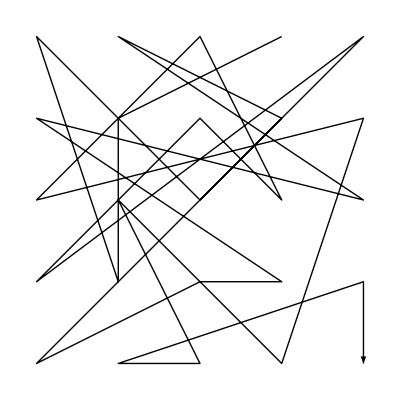
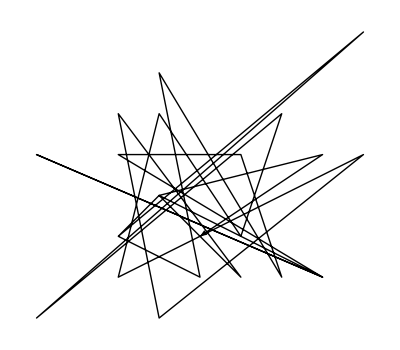
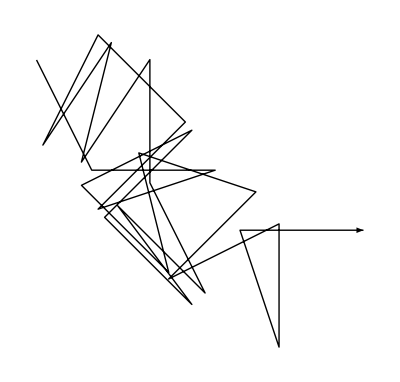
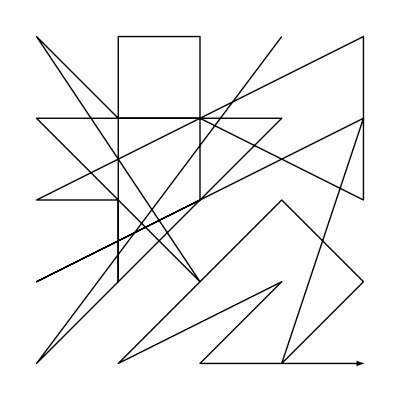
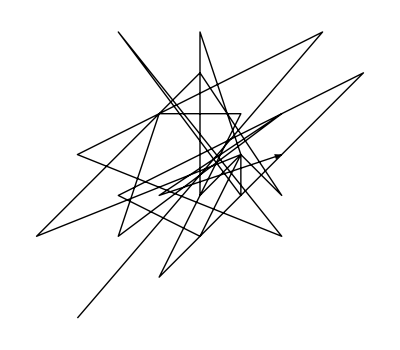
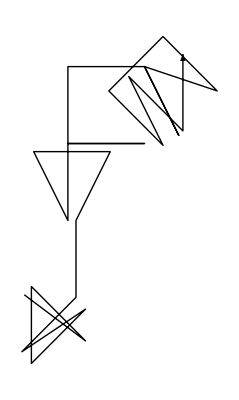
{{(4 | 7 | 17 | 1 | 13
9 | 2 | 15 | 6 | 19
18 | 21 | 5 | 16 | 8
14 | 3 | 11 | 10 | 24
12 | 23 | 22 | 20 | 25),{-Graphics-,{{-2,-1},{0,-2},{-1,3},{2,-2},{1,1},{-2,1},{3,-2},{-4,1},{3,-2},{-1,0},{-2,-1},{4,4},{-4,-3},{2,2},{1,-1},{-1,2},{-2,-2},{4,1},{-1,-3},{-2,2},{1,-2},{-1,0},{3,1},{0,-1}},-Graphics-}},-Graphics-}
{{(6 | 14 | 15 | 1 | 10
4 | 7 | 8 | 3 | 18
11 | 12 | 16 | 21 | 9
17 | 13 | 5 | 23 | 20
2 | 22 | 24 | 19 | 25),{-Graphics-,{{-3,-4},{3,3},{-3,0},{2,-2},{-2,3},{1,-1},{1,0},{2,-1},{0,2},{-4,-2},{1,0},{0,-1},{0,3},{1,0},{0,-2},{-2,-1},{4,2},{-1,-3},{1,1},{-1,1},{-2,-2},{2,1},{-1,-1},{2,0}},-Graphics-}},-Graphics-}

```mathematica
Map[{GM[#],matuni[#]}&,{{{4,7,17,1,13},{9,2,15,6,19},{18,21,5,16,8},{14,3,11,10,24},{12,23,22,20,25}},{{6,14,15,1,10},{4,7,8,3,18},{11,12,16,21,9},{17,13,5,23,20},{2,22,24,19,25}}}]//Column
```

```mathematica
GroupStabilizerChain[MathieuGroupM24[]]
```

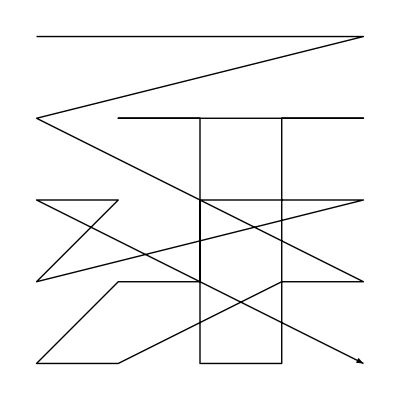
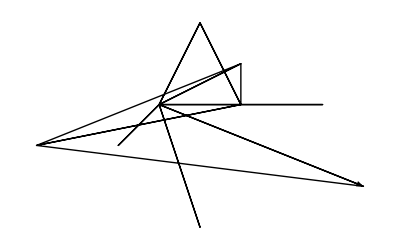
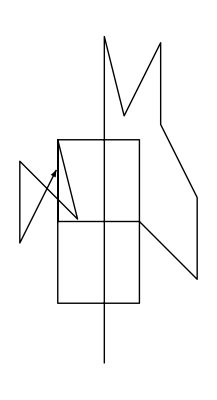
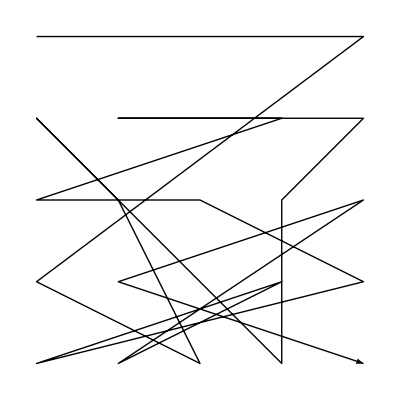
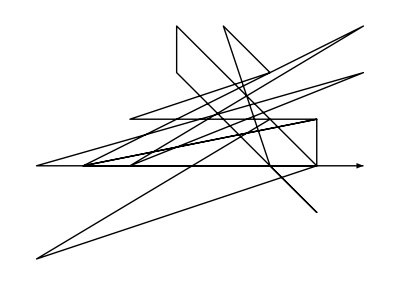
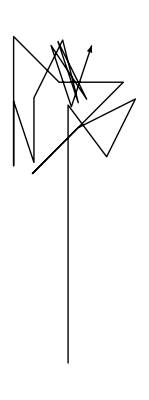
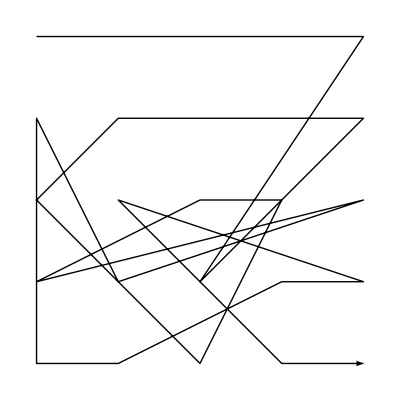
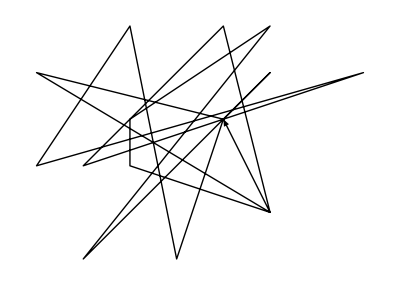
{{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 22
12 | 17 | 24 | 11 | 5
19 | 23 | 13 | 16 | 14
15 | 20 | 18 | 9 | 7
8 | 10 | 6 | 21 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,-1},{-2,-3},{2,1},{-4,-1},{3,1},{-2,-1},{2,3},{-3,0},{2,-1},{2,0},{-4,-1},{3,1},{-2,1},{1,-2},{-2,1},{1,-1},{2,-1},{1,4},{-3,-2},{1,1},{2,-3}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 5 | 17
9 | 16 | 7 | 19 | 18
11 | 23 | 12 | 14 | 22
8 | 4 | 20 | 6 | 10
15 | 21 | 13 | 24 | 25),{-Graphics-,{{1,0},{1,0},{-1,-3},{2,3},{0,-3},{-1,2},{-2,-2},{0,2},{4,-2},{-4,1},{2,0},{0,-2},{1,2},{-3,-2},{1,3},{3,1},{0,-1},{-1,0},{-1,-2},{-1,-1},{3,2},{-3,0},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 15 | 19 | 18
5 | 11 | 23 | 3 | 8
14 | 13 | 9 | 10 | 20
16 | 12 | 24 | 6 | 17
4 | 7 | 22 | 21 | 25),{-Graphics-,{{1,0},{2,-1},{-3,-3},{0,3},{3,-2},{-2,-1},{3,3},{-2,-1},{1,0},{-2,1},{0,-2},{0,1},{-1,0},{2,2},{-2,-3},{4,0},{0,3},{-1,0},{1,-2},{-1,-2},{-1,0},{0,3},{0,-2},{2,-1}},-Graphics-}},-Graphics-},{{(1 | 12 | 6 | 9 | 11
4 | 2 | 15 | 8 | 13
18 | 21 | 3 | 7 | 17
5 | 14 | 19 | 20 | 24
16 | 23 | 10 | 22 | 25),{-Graphics-,{{1,-1},{1,-1},{-2,1},{0,-2},{2,3},{1,-2},{0,1},{0,1},{-1,-4},{2,4},{-3,0},{3,-1},{-3,-2},{1,2},{-2,-3},{4,2},{-4,0},{2,-1},{1,0},{-2,1},{2,-2},{-2,0},{3,1},{0,-1}},-Graphics-}},-Graphics-},{{(6 | 14 | 15 | 1 | 10
4 | 7 | 8 | 3 | 18
11 | 12 | 16 | 21 | 9
17 | 13 | 5 | 23 | 20
2 | 22 | 24 | 19 | 25),{-Graphics-,{{-3,-4},{3,3},{-3,0},{2,-2},{-2,3},{1,-1},{1,0},{2,-1},{0,2},{-4,-2},{1,0},{0,-1},{0,3},{1,0},{0,-2},{-2,-1},{4,2},{-1,-3},{1,1},{-1,1},{-2,-2},{2,1},{-1,-1},{2,0}},-Graphics-}},-Graphics-}},{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 22
12 | 17 | 24 | 11 | 5
19 | 23 | 13 | 16 | 14
15 | 20 | 18 | 9 | 7
8 | 10 | 6 | 21 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,-1},{-2,-3},{2,1},{-4,-1},{3,1},{-2,-1},{2,3},{-3,0},{2,-1},{2,0},{-4,-1},{3,1},{-2,1},{1,-2},{-2,1},{1,-1},{2,-1},{1,4},{-3,-2},{1,1},{2,-3}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 5 | 17
9 | 16 | 7 | 19 | 18
11 | 23 | 12 | 14 | 22
8 | 4 | 20 | 6 | 10
15 | 21 | 13 | 24 | 25),{-Graphics-,{{1,0},{1,0},{-1,-3},{2,3},{0,-3},{-1,2},{-2,-2},{0,2},{4,-2},{-4,1},{2,0},{0,-2},{1,2},{-3,-2},{1,3},{3,1},{0,-1},{-1,0},{-1,-2},{-1,-1},{3,2},{-3,0},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 15 | 19 | 18
5 | 11 | 23 | 3 | 8
14 | 13 | 9 | 10 | 20
16 | 12 | 24 | 6 | 17
4 | 7 | 22 | 21 | 25),{-Graphics-,{{1,0},{2,-1},{-3,-3},{0,3},{3,-2},{-2,-1},{3,3},{-2,-1},{1,0},{-2,1},{0,-2},{0,1},{-1,0},{2,2},{-2,-3},{4,0},{0,3},{-1,0},{1,-2},{-1,-2},{-1,0},{0,3},{0,-2},{2,-1}},-Graphics-}},-Graphics-},{{(1 | 12 | 6 | 9 | 11
4 | 2 | 15 | 8 | 13
18 | 21 | 3 | 7 | 17
5 | 14 | 19 | 20 | 24
16 | 23 | 10 | 22 | 25),{-Graphics-,{{1,-1},{1,-1},{-2,1},{0,-2},{2,3},{1,-2},{0,1},{0,1},{-1,-4},{2,4},{-3,0},{3,-1},{-3,-2},{1,2},{-2,-3},{4,2},{-4,0},{2,-1},{1,0},{-2,1},{2,-2},{-2,0},{3,1},{0,-1}},-Graphics-}},-Graphics-}},{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 22
12 | 17 | 24 | 11 | 5
19 | 23 | 13 | 16 | 14
15 | 20 | 18 | 9 | 7
8 | 10 | 6 | 21 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,-1},{-2,-3},{2,1},{-4,-1},{3,1},{-2,-1},{2,3},{-3,0},{2,-1},{2,0},{-4,-1},{3,1},{-2,1},{1,-2},{-2,1},{1,-1},{2,-1},{1,4},{-3,-2},{1,1},{2,-3}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 5 | 17
9 | 16 | 7 | 19 | 18
11 | 23 | 12 | 14 | 22
8 | 4 | 20 | 6 | 10
15 | 21 | 13 | 24 | 25),{-Graphics-,{{1,0},{1,0},{-1,-3},{2,3},{0,-3},{-1,2},{-2,-2},{0,2},{4,-2},{-4,1},{2,0},{0,-2},{1,2},{-3,-2},{1,3},{3,1},{0,-1},{-1,0},{-1,-2},{-1,-1},{3,2},{-3,0},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 15 | 19 | 18
5 | 11 | 23 | 3 | 8
14 | 13 | 9 | 10 | 20
16 | 12 | 24 | 6 | 17
4 | 7 | 22 | 21 | 25),{-Graphics-,{{1,0},{2,-1},{-3,-3},{0,3},{3,-2},{-2,-1},{3,3},{-2,-1},{1,0},{-2,1},{0,-2},{0,1},{-1,0},{2,2},{-2,-3},{4,0},{0,3},{-1,0},{1,-2},{-1,-2},{-1,0},{0,3},{0,-2},{2,-1}},-Graphics-}},-Graphics-}},{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 22
12 | 17 | 24 | 11 | 5
19 | 23 | 13 | 16 | 14
15 | 20 | 18 | 9 | 7
8 | 10 | 6 | 21 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,-1},{-2,-3},{2,1},{-4,-1},{3,1},{-2,-1},{2,3},{-3,0},{2,-1},{2,0},{-4,-1},{3,1},{-2,1},{1,-2},{-2,1},{1,-1},{2,-1},{1,4},{-3,-2},{1,1},{2,-3}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 5 | 17
9 | 16 | 7 | 19 | 18
11 | 23 | 12 | 14 | 22
8 | 4 | 20 | 6 | 10
15 | 21 | 13 | 24 | 25),{-Graphics-,{{1,0},{1,0},{-1,-3},{2,3},{0,-3},{-1,2},{-2,-2},{0,2},{4,-2},{-4,1},{2,0},{0,-2},{1,2},{-3,-2},{1,3},{3,1},{0,-1},{-1,0},{-1,-2},{-1,-1},{3,2},{-3,0},{2,-2},{1,0}},-Graphics-}},-Graphics-}},{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 22
12 | 17 | 24 | 11 | 5
19 | 23 | 13 | 16 | 14
15 | 20 | 18 | 9 | 7
8 | 10 | 6 | 21 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,-1},{-2,-3},{2,1},{-4,-1},{3,1},{-2,-1},{2,3},{-3,0},{2,-1},{2,0},{-4,-1},{3,1},{-2,1},{1,-2},{-2,1},{1,-1},{2,-1},{1,4},{-3,-2},{1,1},{2,-3}},-Graphics-}},-Graphics-}},{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-},{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-}},{{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-}}}

```mathematica
wdoj[x_]:=Map[{GM[Partition[Permute[Range[25],#],5]],matuni[Partition[Permute[Range[25],#],5]]}&,x]

Map[wdoj,{{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}]}}]
```

```mathematica
DeleteDuplicates[Flatten[{{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}]},{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}]}}]]
```

```mathematica
{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}//Length
```

8

```mathematica
wdoj[{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}]//Column
```

{{(1 | 2 | 3 | 4 | 5
6 | 14 | 13 | 16 | 15
24 | 23 | 19 | 20 | 21
22 | 11 | 12 | 8 | 7
10 | 9 | 18 | 17 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-1},{4,-2},{-1,0},{-2,-1},{-1,0},{1,1},{1,0},{0,2},{-1,0},{3,0},{-1,0},{0,-3},{-1,0},{0,2},{1,0},{1,0},{-4,-1},{1,1},{-1,0},{4,-2}},-Graphics-}},-Graphics-}
{{(1 | 2 | 3 | 4 | 5
9 | 15 | 14 | 16 | 13
17 | 8 | 18 | 12 | 23
6 | 24 | 10 | 21 | 19
20 | 22 | 7 | 11 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-4,-3},{2,-1},{-1,2},{-1,1},{2,-2},{1,-1},{0,2},{1,1},{-2,0},{-1,0},{2,0},{-3,-1},{2,0},{2,-1},{-4,-1},{3,1},{-2,-1},{3,2},{-3,-1},{3,-1}},-Graphics-}},-Graphics-}
{{(1 | 2 | 3 | 4 | 5
18 | 10 | 9 | 8 | 7
11 | 23 | 14 | 13 | 16
15 | 17 | 6 | 21 | 22
19 | 20 | 12 | 24 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,0},{-2,-3},{2,2},{-1,0},{-1,0},{-1,0},{-1,-1},{2,-2},{1,2},{-1,0},{-2,-1},{4,1},{-3,-1},{-1,2},{0,-3},{1,0},{2,1},{1,0},{-3,1},{2,-2},{1,0}},-Graphics-}},-Graphics-}
{{(1 | 2 | 3 | 4 | 22
12 | 17 | 24 | 11 | 5
19 | 23 | 13 | 16 | 14
15 | 20 | 18 | 9 | 7
8 | 10 | 6 | 21 | 25),{-Graphics-,{{1,0},{1,0},{1,0},{1,-1},{-2,-3},{2,1},{-4,-1},{3,1},{-2,-1},{2,3},{-3,0},{2,-1},{2,0},{-4,-1},{3,1},{-2,1},{1,-2},{-2,1},{1,-1},{2,-1},{1,4},{-3,-2},{1,1},{2,-3}},-Graphics-}},-Graphics-}
{{(1 | 2 | 3 | 5 | 17
9 | 16 | 7 | 19 | 18
11 | 23 | 12 | 14 | 22
8 | 4 | 20 | 6 | 10
15 | 21 | 13 | 24 | 25),{-Graphics-,{{1,0},{1,0},{-1,-3},{2,3},{0,-3},{-1,2},{-2,-2},{0,2},{4,-2},{-4,1},{2,0},{0,-2},{1,2},{-3,-2},{1,3},{3,1},{0,-1},{-1,0},{-1,-2},{-1,-1},{3,2},{-3,0},{2,-2},{1,0}},-Graphics-}},-Graphics-}
{{(1 | 2 | 15 | 19 | 18
5 | 11 | 23 | 3 | 8
14 | 13 | 9 | 10 | 20
16 | 12 | 24 | 6 | 17
4 | 7 | 22 | 21 | 25),{-Graphics-,{{1,0},{2,-1},{-3,-3},{0,3},{3,-2},{-2,-1},{3,3},{-2,-1},{1,0},{-2,1},{0,-2},{0,1},{-1,0},{2,2},{-2,-3},{4,0},{0,3},{-1,0},{1,-2},{-1,-2},{-1,0},{0,3},{0,-2},{2,-1}},-Graphics-}},-Graphics-}
{{(1 | 12 | 6 | 9 | 11
4 | 2 | 15 | 8 | 13
18 | 21 | 3 | 7 | 17
5 | 14 | 19 | 20 | 24
16 | 23 | 10 | 22 | 25),{-Graphics-,{{1,-1},{1,-1},{-2,1},{0,-2},{2,3},{1,-2},{0,1},{0,1},{-1,-4},{2,4},{-3,0},{3,-1},{-3,-2},{1,2},{-2,-3},{4,2},{-4,0},{2,-1},{1,0},{-2,1},{2,-2},{-2,0},{3,1},{0,-1}},-Graphics-}},-Graphics-}
{{(6 | 14 | 15 | 1 | 10
4 | 7 | 8 | 3 | 18
11 | 12 | 16 | 21 | 9
17 | 13 | 5 | 23 | 20
2 | 22 | 24 | 19 | 25),{-Graphics-,{{-3,-4},{3,3},{-3,0},{2,-2},{-2,3},{1,-1},{1,0},{2,-1},{0,2},{-4,-2},{1,0},{0,-1},{0,3},{1,0},{0,-2},{-2,-1},{4,2},{-1,-3},{1,1},{-1,1},{-2,-2},{2,1},{-1,-1},{2,0}},-Graphics-}},-Graphics-}

```mathematica
Table[Table[GroupOrder[PermutationGroup[{{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}[[i]],{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}[[j]]}]],{i,1,j}],{j,1,8}]
```

```mathematica
Position[{{3},{12,3},{12,12,2},{48,60,12,3},{960,960,12,168,3},{443520,443520,2520,443520,443520,7},{10200960,10200960,10200960,10200960,10200960,10200960,23},{60480,10200960,336,11520,10200960,322560,244823040,3}},244823040]
```

{{8,7}}

```mathematica
PermutationGroup[{{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}[[8]],{Cycles[{{7,20,14},{8,19,13},{9,22,16},{10,21,15},{11,17,24},{12,18,23}}],Cycles[{{6,16,9},{7,23,15},{8,12,14},{10,18,13},{11,24,17},{19,20,21}}],Cycles[{{6,18},{7,10},{8,9},{12,23},{13,14},{15,16},{19,21},{20,22}}],Cycles[{{5,10,22},{6,23,12},{7,20,17},{8,21,24},{9,19,11},{14,15,16}}],Cycles[{{4,17,5},{6,19,9},{7,8,16},{10,20,18},{12,13,23},{15,21,22}}],Cycles[{{3,9,13,12,17,20,15},{4,21,24,18,5,6,19},{7,22,23,8,10,14,11}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}[[7]]}]
```

PermutationGroup[{Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}]}]

```mathematica
MathieuGroupM24[]//GroupGenerators
```

{Cycles[{{1,4},{2,7},{3,17},{5,13},{6,9},{8,15},{10,19},{11,18},{12,21},{14,16},{20,24},{22,23}}],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]}

```mathematica
Partition[Permute[Range[25],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}]],5]//matuni
```

-Graphics-

```mathematica
Partition[Permute[Range[25],Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}]],5]//matuni
```

-Graphics-

```mathematica
Partition[Permute[Range[25],Cycles[{{1,4},{2,7},{3,17},{5,13},{6,9},{8,15},{10,19},{11,18},{12,21},{14,16},{20,24},{22,23}}]],5]//matuni
```

-Graphics-

```mathematica
Map[{GM[Partition[Permute[Range[25],#],5]],matuni[Partition[Permute[Range[25],#],5]]}&,{Cycles[{{1,4,6},{2,21,14},{3,9,15},{5,18,10},{13,17,16},{19,24,23}}],Cycles[{{2,7,14,17,15,8,9,4,6,3,13,10,23,22,24,20,19,18,11,5,16,21,12}}]}]//Column
```

{{(6 | 14 | 15 | 1 | 10
4 | 7 | 8 | 3 | 18
11 | 12 | 16 | 21 | 9
17 | 13 | 5 | 23 | 20
2 | 22 | 24 | 19 | 25),{-Graphics-,{{-3,-4},{3,3},{-3,0},{2,-2},{-2,3},{1,-1},{1,0},{2,-1},{0,2},{-4,-2},{1,0},{0,-1},{0,3},{1,0},{0,-2},{-2,-1},{4,2},{-1,-3},{1,1},{-1,1},{-2,-2},{2,1},{-1,-1},{2,0}},-Graphics-}},-Graphics-}
{{(1 | 12 | 6 | 9 | 11
4 | 2 | 15 | 8 | 13
18 | 21 | 3 | 7 | 17
5 | 14 | 19 | 20 | 24
16 | 23 | 10 | 22 | 25),{-Graphics-,{{1,-1},{1,-1},{-2,1},{0,-2},{2,3},{1,-2},{0,1},{0,1},{-1,-4},{2,4},{-3,0},{3,-1},{-3,-2},{1,2},{-2,-3},{4,2},{-4,0},{2,-1},{1,0},{-2,1},{2,-2},{-2,0},{3,1},{0,-1}},-Graphics-}},-Graphics-}

```mathematica
16*4*2
100*2
```

128

200

```mathematica
Map[Partition[Permute[Range[100],#],10]&,{Cycles[{{1,84},{2,20},{3,48},{4,56},{5,82},{6,67},{7,55},{8,41},{9,35},{10,40},{11,78},{12,100},{13,49},{14,37},{15,94},{16,76},{17,19},{18,44},{21,34},{22,85},{23,92},{24,57},{25,75},{26,28},{27,64},{29,90},{30,97},{31,38},{32,68},{33,69},{36,53},{39,61},{42,73},{43,91},{45,86},{46,81},{47,89},{50,93},{51,96},{52,72},{54,74},{58,99},{59,95},{60,63},{62,83},{65,70},{66,88},{71,87},{77,98},{79,80}}],Cycles[{{1,80,22},{2,9,11},{3,53,87},{4,23,78},{5,51,18},{6,37,24},{8,27,60},{10,62,47},{12,65,31},{13,64,19},{14,61,52},{15,98,25},{16,73,32},{17,39,33},{20,97,58},{21,96,67},{26,93,99},{28,57,35},{29,71,55},{30,69,45},{34,86,82},{38,59,94},{40,43,91},{42,68,44},{46,85,89},{48,76,90},{49,92,77},{50,66,88},{54,95,56},{63,74,72},{70,81,75},{79,100,83}}]}]
```

{{{84,20,48,56,82,67,55,41,35,40},{78,100,49,37,94,76,19,44,17,2},{34,85,92,57,75,28,64,26,90,97},{38,68,69,21,9,53,14,31,61,10},{8,73,91,18,86,81,89,3,13,93},{96,72,36,74,7,4,24,99,95,63},{39,83,60,27,70,88,6,32,33,65},{87,52,42,54,25,16,98,11,80,79},{46,5,62,1,22,45,71,66,47,29},{43,23,50,15,59,51,30,77,58,12}},{{22,11,87,78,18,24,7,60,2,47},{9,31,19,52,25,32,33,51,64,58},{67,80,4,37,98,99,8,35,55,45},{65,73,39,82,57,36,6,94,17,91},{41,44,40,68,69,89,62,90,77,88},{5,61,3,56,71,95,28,97,38,27},{14,10,72,13,12,50,96,42,30,75},{29,74,16,63,81,48,92,23,83,1},{70,86,100,84,46,34,53,66,85,76},{43,49,26,59,54,21,20,15,93,79}}}

```mathematica
Map[{GM[#],matuni[#]}&,%]//Column
```

{{(84 | 20 | 48 | 56 | 82 | 67 | 55 | 41 | 35 | 40
78 | 100 | 49 | 37 | 94 | 76 | 19 | 44 | 17 | 2
34 | 85 | 92 | 57 | 75 | 28 | 64 | 26 | 90 | 97
38 | 68 | 69 | 21 | 9 | 53 | 14 | 31 | 61 | 10
8 | 73 | 91 | 18 | 86 | 81 | 89 | 3 | 13 | 93
96 | 72 | 36 | 74 | 7 | 4 | 24 | 99 | 95 | 63
39 | 83 | 60 | 27 | 70 | 88 | 6 | 32 | 33 | 65
87 | 52 | 42 | 54 | 25 | 16 | 98 | 11 | 80 | 79
46 | 5 | 62 | 1 | 22 | 45 | 71 | 66 | 47 | 29
43 | 23 | 50 | 15 | 59 | 51 | 30 | 77 | 58 | 12),{-Graphics-,{{6,7},{-2,-3},{-2,-1},{-4,-3},{5,2},{-2,1},{-4,1},{4,1},{5,0},{-2,-4},{2,-2},{-1,5},{-2,1},{-3,-6},{2,2},{3,6},{-5,-3},{3,3},{-5,1},{2,-3},{1,-5},{-3,-1},{5,4},{-2,-2},{3,5},{-4,-4},{2,4},{4,-6},{-3,-1},{1,6},{0,-3},{1,0},{-8,4},{8,2},{-6,-5},{1,4},{-3,-2},{0,-3},{9,6},{-2,0},{-5,-7},{-2,-2},{7,8},{-2,-7},{-5,0},{8,0},{-6,8},{0,-1},{0,-8},{3,0},{-4,2},{4,4},{-2,-4},{3,7},{-3,0},{0,-2},{5,-7},{-4,0},{-2,3},{6,3},{-6,-5},{7,3},{-3,3},{3,-4},{-2,-2},{-2,8},{-4,-3},{1,0},{2,-3},{2,-2},{-5,3},{0,1},{2,-1},{1,3},{1,1},{2,-8},{-7,8},{9,-6},{-1,0},{-3,3},{-1,4},{-3,-6},{-1,6},{1,-2},{3,-2},{-4,-3},{5,1},{1,2},{2,2},{-6,-2},{0,2},{7,-2},{-5,3},{4,-4},{-8,0},{9,3},{-3,-5},{1,2},{-6,4}},-Graphics-}},-Graphics-}
{{(22 | 11 | 87 | 78 | 18 | 24 | 7 | 60 | 2 | 47
9 | 31 | 19 | 52 | 25 | 32 | 33 | 51 | 64 | 58
67 | 80 | 4 | 37 | 98 | 99 | 8 | 35 | 55 | 45
65 | 73 | 39 | 82 | 57 | 36 | 6 | 94 | 17 | 91
41 | 44 | 40 | 68 | 69 | 89 | 62 | 90 | 77 | 88
5 | 61 | 3 | 56 | 71 | 95 | 28 | 97 | 38 | 27
14 | 10 | 72 | 13 | 12 | 50 | 96 | 42 | 30 | 75
29 | 74 | 16 | 63 | 81 | 48 | 92 | 23 | 83 | 1
70 | 86 | 100 | 84 | 46 | 34 | 53 | 66 | 85 | 76
43 | 49 | 26 | 59 | 54 | 21 | 20 | 15 | 93 | 79),{-Graphics-,{{-1,7},{-6,-5},{0,3},{-2,-3},{6,2},{0,3},{0,-2},{-6,1},{1,-5},{0,6},{3,-6},{-1,0},{-3,0},{7,-3},{-5,2},{6,4},{-4,3},{-2,-1},{4,-8},{-1,0},{-5,9},{7,-7},{-2,7},{-1,-1},{-2,-8},{7,4},{-3,0},{-6,-2},{8,1},{-7,5},{4,0},{1,0},{-1,-7},{2,6},{-2,-1},{-2,1},{5,-3},{-6,2},{0,-1},{-2,0},{7,-2},{-7,-3},{1,5},{8,2},{-5,-6},{5,8},{-4,-7},{-4,-2},{4,3},{2,5},{-4,0},{3,-7},{-2,-1},{4,7},{-5,-3},{1,2},{5,2},{-6,-8},{4,9},{-6,-5},{5,1},{-3,-3},{5,6},{-8,-2},{7,-5},{-7,6},{3,-2},{1,0},{-4,-4},{4,3},{-2,-1},{-1,3},{0,-4},{8,1},{0,-2},{-1,4},{-5,4},{6,-9},{-8,7},{3,-5},{-1,4},{5,-4},{-5,-1},{5,0},{-7,0},{1,8},{7,-4},{-4,0},{2,0},{2,1},{-3,-4},{2,-2},{-1,6},{-2,-2},{1,-1},{1,1},{-3,3},{1,0},{-3,-6}},-Graphics-}},-Graphics-}

```mathematica
McLaughlinGroupMcL[]//GroupGenerators
```

```mathematica
Map[Partition[Permute[Range[289],#],17]&,{Cycles[{{1,191},{2,182},{4,81},{5,55},{6,60},{8,66},{9,272},{10,177},{11,192},{12,163},{14,242},{15,133},{16,107},{18,267},{19,108},{20,218},{21,198},{22,185},{23,211},{24,82},{25,204},{26,195},{27,132},{28,253},{29,207},{30,59},{31,179},{32,154},{33,264},{34,152},{35,92},{36,189},{37,217},{38,197},{39,85},{40,156},{42,184},{43,102},{44,50},{45,216},{46,99},{47,181},{49,199},{51,111},{53,158},{54,236},{56,210},{58,103},{61,263},{63,119},{64,138},{65,127},{67,105},{68,137},{70,125},{71,144},{72,219},{73,261},{75,175},{77,269},{78,237},{79,268},{83,232},{84,256},{86,104},{87,95},{89,234},{90,233},{91,140},{94,149},{97,173},{98,160},{100,112},{101,123},{106,221},{109,131},{110,176},{113,262},{114,257},{115,201},{117,260},{118,238},{120,275},{121,214},{122,225},{124,246},{126,170},{129,141},{134,196},{135,167},{142,235},{143,224},{145,205},{146,249},{148,226},{150,243},{153,193},{155,228},{161,231},{164,215},{165,180},{168,222},{169,270},{171,241},{172,259},{174,212},{178,188},{183,266},{186,203},{190,250},{202,247},{208,255},{209,251},{213,252},{223,271},{227,274},{230,240},{239,254},{245,258},{265,273}}],Cycles[{{1,24,204,92,155},{2,28,272,165,78},{3,67,142,31,255},{4,168,77,17,100},{5,118,19,223,211},{6,274,137,79,245},{7,98,75,73,14},{8,209,43,139,193},{9,266,104,70,145},{10,271,12,13,71},{11,247,138,121,269},{15,218,133,164,196},{16,170,182,65,171},{18,26,198,124,185},{20,128,159,83,38},{21,264,27,64,162},{22,116,53,101,51},{23,179,244,80,203},{25,40,177,85,191},{29,56,135,68,195},{30,132,42,248,146},{32,148,114,49,134},{33,61,163,90,227},{34,241,233,95,181},{35,89,82,205,41},{36,239,275,257,183},{37,54,99,249,176},{39,126,189,136,230},{44,172,153,125,119},{45,234,222,232,212},{46,214,69,167,190},{47,140,268,174,62},{48,55,113,220,235},{50,213,224,202,130},{52,107,262,226,88},{57,221,261,129,58},{59,252,260,216,166},{60,84,188,208,201},{63,94,173,210,81},{66,192,93,169,110},{72,152,197,217,254},{74,206,154,186,219},{76,91,180,238,112},{86,215,231,131,225},{87,115,158,178,240},{96,265,161,120,144},{97,250,243,263,109},{102,207,246,122,127},{103,156,160,151,150},{105,267,199,111,117},{106,273,242,149,143},{108,256,157,147,184},{123,141,259,175,200},{187,251,258,194,236},{228,237,253,270,229}}]}]
```

{{{191,182,3,81,55,60,7,66,272,177,192,163,13,242,133,107,17},{267,108,218,198,185,211,82,204,195,132,253,207,59,179,154,264,152},{92,189,217,197,85,156,41,184,102,50,216,99,181,48,199,44,111},{52,158,236,5,210,57,103,30,6,263,62,119,138,127,8,105,137},{69,125,144,219,261,74,175,76,269,237,268,80,4,24,232,256,39},{104,95,88,234,233,140,35,93,149,87,96,173,160,46,112,123,43},{58,86,67,221,16,19,131,176,51,100,262,257,201,116,260,238,63},{275,214,225,101,246,70,170,65,128,141,130,109,27,15,196,167,136},{68,64,139,91,129,235,224,71,205,249,147,226,94,243,151,34,193},{32,228,40,157,53,159,98,231,162,12,215,180,166,135,222,270,126},{241,259,97,212,75,110,10,188,31,165,47,2,266,42,22,203,187},{178,36,250,1,11,153,194,26,134,38,21,49,200,115,247,186,25},{145,206,29,255,251,56,23,174,252,121,164,45,37,20,72,220,106},{168,271,143,122,148,274,155,229,240,161,83,90,89,142,54,78,118},{254,230,171,14,150,244,258,124,202,248,146,190,209,213,28,239,208},{84,114,245,172,117,73,113,61,33,273,183,18,79,77,169,223,9},{265,227,120,276,277,278,279,280,281,282,283,284,285,286,287,288,289}},{{155,78,255,100,211,245,14,193,145,71,269,271,12,73,196,171,77},{185,118,38,162,51,203,1,191,18,264,2,195,146,142,134,227,181},{41,183,176,83,230,25,205,132,209,119,212,190,62,235,114,130,101},{88,116,37,48,29,58,129,166,201,33,174,81,27,182,110,3,135},{214,104,13,254,75,219,98,112,168,165,137,244,210,89,159,60,177},{225,240,226,35,163,76,204,192,63,233,144,109,7,54,17,53,127},{150,266,117,143,52,184,263,169,199,238,55,148,87,22,111,5,125},{161,138,246,200,198,153,39,122,20,261,202,231,30,218,49,56,189},{274,247,43,47,123,67,149,120,70,248,157,32,242,151,160,72,172},{206,92,103,256,115,128,156,265,64,61,133,272,216,69,4,93,16},{65,44,94,268,259,249,40,158,23,91,95,170,257,147,124,154,236},{84,126,167,85,66,139,258,68,164,152,26,267,175,208,224,80,24},{82,74,102,188,8,173,223,232,50,46,86,260,197,15,186,113,57},{234,19,213,131,262,90,229,270,136,215,222,241,45,220,194,228,180},{36,178,34,273,250,179,79,207,11,42,99,97,187,59,237,217,31},{108,275,251,141,252,221,107,243,21,96,9,105,140,121,253,10,28},{106,6,239,276,277,278,279,280,281,282,283,284,285,286,287,288,289}}}

```mathematica
Map[{GM[#],matuni[#]}&,%]//Column
```

```mathematica
{{□}, {□}}
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Sqrt[1782]//N
```

42.2137

```mathematica
43^2
```

1849

```mathematica
Map[Partition[Permute[Range[1849],#],43]&,{Cycles[{{1,191},{2,182},{4,81},{5,55},{6,60},{8,66},{9,272},{10,177},{11,192},{12,163},{14,242},{15,133},{16,107},{18,267},{19,108},{20,218},{21,198},{22,185},{23,211},{24,82},{25,204},{26,195},{27,132},{28,253},{29,207},{30,59},{31,179},{32,154},{33,264},{34,152},{35,92},{36,189},{37,217},{38,197},{39,85},{40,156},{42,184},{43,102},{44,50},{45,216},{46,99},{47,181},{49,199},{51,111},{53,158},{54,236},{56,210},{58,103},{61,263},{63,119},{64,138},{65,127},{67,105},{68,137},{70,125},{71,144},{72,219},{73,261},{75,175},{77,269},{78,237},{79,268},{83,232},{84,256},{86,104},{87,95},{89,234},{90,233},{91,140},{94,149},{97,173},{98,160},{100,112},{101,123},{106,221},{109,131},{110,176},{113,262},{114,257},{115,201},{117,260},{118,238},{120,275},{121,214},{122,225},{124,246},{126,170},{129,141},{134,196},{135,167},{142,235},{143,224},{145,205},{146,249},{148,226},{150,243},{153,193},{155,228},{161,231},{164,215},{165,180},{168,222},{169,270},{171,241},{172,259},{174,212},{178,188},{183,266},{186,203},{190,250},{202,247},{208,255},{209,251},{213,252},{223,271},{227,274},{230,240},{239,254},{245,258},{265,273}}],Cycles[{{1,24,204,92,155},{2,28,272,165,78},{3,67,142,31,255},{4,168,77,17,100},{5,118,19,223,211},{6,274,137,79,245},{7,98,75,73,14},{8,209,43,139,193},{9,266,104,70,145},{10,271,12,13,71},{11,247,138,121,269},{15,218,133,164,196},{16,170,182,65,171},{18,26,198,124,185},{20,128,159,83,38},{21,264,27,64,162},{22,116,53,101,51},{23,179,244,80,203},{25,40,177,85,191},{29,56,135,68,195},{30,132,42,248,146},{32,148,114,49,134},{33,61,163,90,227},{34,241,233,95,181},{35,89,82,205,41},{36,239,275,257,183},{37,54,99,249,176},{39,126,189,136,230},{44,172,153,125,119},{45,234,222,232,212},{46,214,69,167,190},{47,140,268,174,62},{48,55,113,220,235},{50,213,224,202,130},{52,107,262,226,88},{57,221,261,129,58},{59,252,260,216,166},{60,84,188,208,201},{63,94,173,210,81},{66,192,93,169,110},{72,152,197,217,254},{74,206,154,186,219},{76,91,180,238,112},{86,215,231,131,225},{87,115,158,178,240},{96,265,161,120,144},{97,250,243,263,109},{102,207,246,122,127},{103,156,160,151,150},{105,267,199,111,117},{106,273,242,149,143},{108,256,157,147,184},{123,141,259,175,200},{187,251,258,194,236},{228,237,253,270,229}}]}]
```

{{{191,182,3,81,55,60,7,66,272,177,192,163,13,242,133,107,17,267,108,218,198,185,211,82,204,195,132,253,207,59,179,154,264,152,92,189,217,197,85,156,41,184,102},{50,216,99,181,48,199,44,111,52,158,236,5,210,57,103,30,6,263,62,119,138,127,8,105,137,69,125,144,219,261,74,175,76,269,237,268,80,4,24,232,256,39,104},{95,88,234,233,140,35,93,149,87,96,173,160,46,112,123,43,58,86,67,221,16,19,131,176,51,100,262,257,201,116,260,238,63,275,214,225,101,246,70,170,65,128,141},{130,109,27,15,196,167,136,68,64,139,91,129,235,224,71,205,249,147,226,94,243,151,34,193,32,228,40,157,53,159,98,231,162,12,215,180,166,135,222,270,126,241,259},{97,212,75,110,10,188,31,165,47,2,266,42,22,203,187,178,36,250,1,11,153,194,26,134,38,21,49,200,115,247,186,25,145,206,29,255,251,56,23,174,252,121,164},{45,37,20,72,220,106,168,271,143,122,148,274,155,229,240,161,83,90,89,142,54,78,118,254,230,171,14,150,244,258,124,202,248,146,190,209,213,28,239,208,84,114,245},{172,117,73,113,61,33,273,183,18,79,77,169,223,9,265,227,120,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301},{302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344},{345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387},{388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430},{431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473},{474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516},{517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559},{560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602},{603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645},{646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688},{689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731},{732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774},{775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817},{818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860},{861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903},{904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946},{947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989},{990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032},{1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075},{1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118},{1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161},{1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204},{1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247},{1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290},{1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333},{1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376},{1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419},{1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462},{1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505},{1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548},{1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591},{1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634},{1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677},{1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720},{1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763},{1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806},{1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849}},{{155,78,255,100,211,245,14,193,145,71,269,271,12,73,196,171,77,185,118,38,162,51,203,1,191,18,264,2,195,146,142,134,227,181,41,183,176,83,230,25,205,132,209},{119,212,190,62,235,114,130,101,88,116,37,48,29,58,129,166,201,33,174,81,27,182,110,3,135,214,104,13,254,75,219,98,112,168,165,137,244,210,89,159,60,177,225},{240,226,35,163,76,204,192,63,233,144,109,7,54,17,53,127,150,266,117,143,52,184,263,169,199,238,55,148,87,22,111,5,125,161,138,246,200,198,153,39,122,20,261},{202,231,30,218,49,56,189,274,247,43,47,123,67,149,120,70,248,157,32,242,151,160,72,172,206,92,103,256,115,128,156,265,64,61,133,272,216,69,4,93,16,65,44},{94,268,259,249,40,158,23,91,95,170,257,147,124,154,236,84,126,167,85,66,139,258,68,164,152,26,267,175,208,224,80,24,82,74,102,188,8,173,223,232,50,46,86},{260,197,15,186,113,57,234,19,213,131,262,90,229,270,136,215,222,241,45,220,194,228,180,36,178,34,273,250,179,79,207,11,42,99,97,187,59,237,217,31,108,275,251},{141,252,221,107,243,21,96,9,105,140,121,253,10,28,106,6,239,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301},{302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344},{345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387},{388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430},{431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473},{474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516},{517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559},{560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602},{603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645},{646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688},{689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731},{732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774},{775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817},{818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860},{861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903},{904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946},{947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989},{990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032},{1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075},{1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118},{1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161},{1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204},{1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247},{1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290},{1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333},{1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376},{1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419},{1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462},{1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505},{1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548},{1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591},{1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634},{1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677},{1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720},{1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763},{1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806},{1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849}}}

```mathematica
Map[{Last[Last[GM[#]]],matuni[#]}&,%]//Column
```